## Background

```mathematica
<<MaTeX`
SetOptions[MaTeX,FontSize->12,Magnification->1,"DisplayStyle"->True]
style=Directive[FontFamily->"LM Roman 12",FontSize->10];
cm=72/2.54;
(* http://ksrowell.com/blog-visualizing-data/2012/02/02/optimal-colors-for-graphs/ *)
col1 = RGBColor[57/256, 106/256, 177/256]
col2 = RGBColor[218/256, 124/256, 48/256]
col3= RGBColor[62/256, 150/256, 81/256]
col4 = RGBColor[204/256, 37/256, 41/256]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

RGBColor[Rational[57, 256], Rational[53, 128], Rational[177, 256]]

RGBColor[Rational[109, 128], Rational[31, 64], Rational[3, 16]]

RGBColor[Rational[31, 128], Rational[75, 128], Rational[81, 256]]

RGBColor[Rational[51, 64], Rational[37, 256], Rational[41, 256]]

```mathematica
(*fs1=15;
fs2=10;
fig1 = ListLogPlot[
{
llist10, 
llist13,
llist20,
llist23,
llist30,
llist33,
llist40,
llist43
},
Joined->True,
PlotStyle->{col1, {col1, Dashed}, col2, {col2, Dashed}, col3, {col3, Dashed}, col4, {col4, Dashed}},
PlotRange->{{0, 1}, All},
Frame->True,
ImageSize->8.6cm,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\Delta_r", ContentPadding->False, FontSize->fs1],
MaTeX["\\text{Signature length } \\tilde{L}", ContentPadding->False, FontSize->fs1]},

FrameTicks->{{{
{10^0, MaTeX["10^0", ContentPadding->False, FontSize->fs2]},
{10^1, MaTeX["10^1", ContentPadding->False, FontSize->fs2]},
{10^2, MaTeX["10^2", ContentPadding->False, FontSize->fs2]},
{10^3, MaTeX["10^3", ContentPadding->False, FontSize->fs2]},
{10^4, MaTeX["10^4", ContentPadding->False, FontSize->fs2]},
{10^5, MaTeX[" 1 \\times 10^5", ContentPadding->False, FontSize->fs2]},
{2*10^5, MaTeX["2 \\times 10^5", ContentPadding->False, FontSize->fs2]},
{3*10^5, MaTeX["3 \\times 10^5", ContentPadding->False, FontSize->fs2]},
{4*10^5, MaTeX["4 \\times 10^5", ContentPadding->False, FontSize->fs2]},
{10^6, MaTeX["10^6", ContentPadding->False, FontSize->fs2]},
{10^7, MaTeX["10^7", ContentPadding->False, FontSize->fs2]},
{10^8, MaTeX["10^8", ContentPadding->False, FontSize->fs2]},
{10^9, MaTeX["10^9", ContentPadding->False, FontSize->fs2]}

}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]}, 
{0.2, MaTeX["0.2", ContentPadding->False, FontSize->fs2]},
{0.4, MaTeX["0.4", ContentPadding->False, FontSize->fs2]}, 
{0.6, MaTeX["0.6", ContentPadding->False, FontSize->fs2]},
{0.8, MaTeX["0.8", ContentPadding->False, FontSize->fs2]},{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
}, None}}

];
fig1~Magnify~1*)
```

Making lists

## Mutual Information

### Honest Bob/Charlie

```mathematica
(*honestMutInf[gglob_, hglob_, cohampb_, cohampc_, Tb_, Tc_, nb_, nc_]*)
```

gglob = 0.5 = hglob.
Tb=Tc;
nb=nc=0;
Varying αb and αc:

```mathematica
gin = 0.5;
hin = 0.5;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
```

```mathematica
Plot3D[honestMutInf[gin, hin, αb, αc, Tbin, Tcin, nbin ,ncin], {αb, 0.01, 1.0}, {αc, 0.01, 1.0}]//AbsoluteTiming
```

$Aborted

```mathematica
αlist =Join[{0.01}, Range[0.1, 3.0, 0.25]];
```

```mathematica
Length[αlist]^2
```

169

```mathematica
Now
graph1list = ParallelTable[{αb, αc, honestMutInf[gin, hin, αb, αc, Tbin, Tcin, nbin ,ncin]}, 
{αb, αlist}, {αc, αlist}]
Now
```

Tue 3 Mar 2020 12:14:21GMT

{{{0.01,0.01,0.00566},{0.01,0.1,0.00988},{0.01,0.35,0.05704},{0.01,0.6,0.1516},{0.01,0.85,0.2841},{0.01,1.1,0.44395},{0.01,1.35,0.62143},{0.01,1.6,0.80794},{0.01,1.85,0.98865},{0.01,2.1,1.1592},{0.01,2.35,1.3147},{0.01,2.6,1.4517},{0.01,2.85,1.5693}},{{0.1,0.01,0.00988},{0.1,0.1,0.0141},{0.1,0.35,0.06112},{0.1,0.6,0.1554},{0.1,0.85,0.2876},{0.1,1.1,0.44705},{0.1,1.35,0.62423},{0.1,1.6,0.81046},{0.1,1.85,0.99098},{0.1,2.1,1.1615},{0.1,2.35,1.3169},{0.1,2.6,1.454},{0.1,2.85,1.5718}},{{0.35,0.01,0.05704},{0.35,0.1,0.06112},{0.35,0.35,0.1066},{0.35,0.6,0.1979},{0.35,0.85,0.3263},{0.35,1.1,0.41818},{0.35,1.35,0.65556},{0.35,1.6,0.83877},{0.35,1.85,1.0171},{0.35,2.1,1.1864},{0.35,2.35,1.3419},{0.35,2.6,1.4798},{0.35,2.85,1.5991}},{{0.6,0.01,0.1516},{0.6,0.1,0.1554},{0.6,0.35,0.1979},{0.6,0.6,0.2836},{0.6,0.85,0.40523},{0.6,1.1,0.55204},{0.6,1.35,0.72204},{0.6,1.6,0.89629},{0.6,1.85,1.07},{0.6,2.1,1.2366},{0.6,2.35,1.3916},{0.6,2.6,1.5311},{0.6,2.85,1.6532}},{{0.85,0.01,0.2841},{0.85,0.1,0.2876},{0.85,0.35,0.3263},{0.85,0.6,0.40523},{0.85,0.85,0.51648},{0.85,1.1,0.65268},{0.85,1.35,0.80544},{0.85,1.6,0.97888},{0.85,1.85,1.1466},{0.85,2.1,1.309},{0.85,2.35,1.4622},{0.85,2.6,1.6024},{0.85,2.85,1.7279}},{{1.1,0.01,0.44395},{1.1,0.1,0.44705},{1.1,0.35,0.41818},{1.1,0.6,0.55204},{1.1,0.85,0.65268},{1.1,1.1,0.77703},{1.1,1.35,0.91814},{1.1,1.6,1.0694},{1.1,1.85,1.2408},{1.1,2.1,1.3969},{1.1,2.35,1.5089},{1.1,2.6,1.6871},{1.1,2.85,1.8153}},{{1.35,0.01,0.62143},{1.35,0.1,0.62423},{1.35,0.35,0.65556},{1.35,0.6,0.72204},{1.35,0.85,0.80544},{1.35,1.1,0.91814},{1.35,1.35,1.0597},{1.35,1.6,1.2013},{1.35,1.85,1.3149},{1.35,2.1,1.496},{1.35,2.35,1.6408},{1.35,2.6,1.7788},{1.35,2.85,1.9082}},{{1.6,0.01,0.80794},{1.6,0.1,0.81046},{1.6,0.35,0.83877},{1.6,0.6,0.89629},{1.6,0.85,0.97888},{1.6,1.1,1.0694},{1.6,1.35,1.2013},{1.6,1.6,1.2969},{1.6,1.85,1.465},{1.6,2.1,1.6024},{1.6,2.35,1.7394},{1.6,2.6,1.8726},{1.6,2.85,2.00066}},{{1.85,0.01,0.98865},{1.85,0.1,0.99098},{1.85,0.35,1.0171},{1.85,0.6,1.07},{1.85,0.85,1.1466},{1.85,1.1,1.2408},{1.85,1.35,1.3149},{1.85,1.6,1.465},{1.85,1.85,1.5875},{1.85,2.1,1.7133},{1.85,2.35,1.8402},{1.85,2.6,1.9666},{1.85,2.85,2.08903}},{{2.1,0.01,1.1592},{2.1,0.1,1.1615},{2.1,0.35,1.1864},{2.1,0.6,1.2366},{2.1,0.85,1.309},{2.1,1.1,1.3969},{2.1,1.35,1.496},{2.1,1.6,1.6024},{2.1,1.85,1.7133},{2.1,2.1,1.8268},{2.1,2.35,1.9406},{2.1,2.6,2.05771},{2.1,2.85,2.17313}},{{2.35,0.01,1.3147},{2.35,0.1,1.3169},{2.35,0.35,1.3419},{2.35,0.6,1.3916},{2.35,0.85,1.4622},{2.35,1.1,1.5089},{2.35,1.35,1.6408},{2.35,1.6,1.7394},{2.35,1.85,1.8402},{2.35,2.1,1.9406},{2.35,2.35,2.04415},{2.35,2.6,2.14738},{2.35,2.85,2.25651}},{{2.6,0.01,1.4517},{2.6,0.1,1.454},{2.6,0.35,1.4798},{2.6,0.6,1.5311},{2.6,0.85,1.6024},{2.6,1.1,1.6871},{2.6,1.35,1.7788},{2.6,1.6,1.8726},{2.6,1.85,1.9666},{2.6,2.1,2.05771},{2.6,2.35,2.14738},{2.6,2.6,2.24153},{2.6,2.85,2.32716}},{{2.85,0.01,1.5693},{2.85,0.1,1.5718},{2.85,0.35,1.5991},{2.85,0.6,1.6532},{2.85,0.85,1.7279},{2.85,1.1,1.8153},{2.85,1.35,1.9082},{2.85,1.6,2.00066},{2.85,1.85,2.08903},{2.85,2.1,2.17313},{2.85,2.35,2.25651},{2.85,2.6,2.32716},{2.85,2.85,2.40078}}}

Tue 3 Mar 2020 12:18:55GMT

```mathematica
ListPlot3D[graph1list~Flatten~1]
```

-Graphics3D-

```mathematica
Tlist = Join[{0.01}, Range[0.1, 0.9, 0.1], {0.99}];
```

```mathematica
graph1list2 = ParallelTable[{α, T, honestMutInf[gin, hin, α, α, T, T, nbin ,ncin]}, 
{α, αlist}, {T, Tlist}]
Now
```

{{{0.01,0.01,0.00557},{0.01,0.1,0.00558},{0.01,0.2,0.0056},{0.01,0.3,0.00561},{0.01,0.4,0.00563},{0.01,0.5,0.00564},{0.01,0.6,0.00566},{0.01,0.7,0.00567},{0.01,0.8,0.00568},{0.01,0.9,0.0057},{0.01,0.99,0.00571}},{{0.1,0.01,0.00571},{0.1,0.1,0.007},{0.1,0.2,0.00842},{0.1,0.3,0.00984},{0.1,0.4,0.0113},{0.1,0.5,0.0127},{0.1,0.6,0.0141},{0.1,0.7,0.0155},{0.1,0.8,0.0169},{0.1,0.9,0.0183},{0.1,0.99,0.0196}},{{0.35,0.01,0.00732},{0.35,0.1,0.0229},{0.35,0.2,0.04008},{0.35,0.3,0.05701},{0.35,0.4,0.07374},{0.35,0.5,0.09027},{0.35,0.6,0.1066},{0.35,0.7,0.1227},{0.35,0.8,0.1387},{0.35,0.9,0.1545},{0.35,0.99,0.1685}},{{0.6,0.01,0.0107},{0.6,0.1,0.05598},{0.6,0.2,0.1046},{0.6,0.3,0.1516},{0.6,0.4,0.197},{0.6,0.5,0.241},{0.6,0.6,0.2836},{0.6,0.7,0.3249},{0.6,0.8,0.36563},{0.6,0.9,0.40454},{0.6,0.99,0.42617}},{{0.85,0.01,0.0158},{0.85,0.1,0.1049},{0.85,0.2,0.1976},{0.85,0.3,0.2845},{0.85,0.4,0.36672},{0.85,0.5,0.43127},{0.85,0.6,0.51648},{0.85,0.7,0.58561},{0.85,0.8,0.65139},{0.85,0.9,0.71416},{0.85,0.99,0.7683}},{{1.1,0.01,0.0227},{1.1,0.1,0.1682},{1.1,0.2,0.3136},{1.1,0.3,0.43855},{1.1,0.4,0.56516},{1.1,0.5,0.67519},{1.1,0.6,0.77703},{1.1,0.7,0.8719},{1.1,0.8,0.96074},{1.1,0.9,1.0443},{1.1,0.99,1.1286}},{{1.35,0.01,0.0313},{1.35,0.1,0.2437},{1.35,0.2,0.44702},{1.35,0.3,0.62333},{1.35,0.4,0.77947},{1.35,0.5,0.91971},{1.35,0.6,1.0597},{1.35,0.7,1.1778},{1.35,0.8,1.2863},{1.35,0.9,1.3863},{1.35,0.99,1.4701}},{{1.6,0.01,0.0416},{1.6,0.1,0.3294},{1.6,0.2,0.59142},{1.6,0.3,0.8107},{1.6,0.4,1.},{1.6,0.5,1.1805},{1.6,0.6,1.2969},{1.6,0.7,1.4641},{1.6,0.8,1.585},{1.6,0.9,1.6949},{1.6,0.99,1.7855}},{{1.85,0.01,0.05354},{1.85,0.1,0.41117},{1.85,0.2,0.74295},{1.85,0.3,1.0019},{1.85,0.4,1.2344},{1.85,0.5,1.4233},{1.85,0.6,1.5875},{1.85,0.7,1.7318},{1.85,0.8,1.8597},{1.85,0.9,1.9728},{1.85,0.99,2.06567}},{{2.1,0.01,0.06707},{2.1,0.1,0.52382},{2.1,0.2,0.8981},{2.1,0.3,1.2068},{2.1,0.4,1.4501},{2.1,0.5,1.6536},{2.1,0.6,1.8268},{2.1,0.7,1.9749},{2.1,0.8,2.10453},{2.1,0.9,2.22108},{2.1,0.99,2.30456}},{{2.35,0.01,0.08217},{2.35,0.1,0.62831},{2.35,0.2,1.0672},{2.35,0.3,1.395},{2.35,0.4,1.6553},{2.35,0.5,1.8678},{2.35,0.6,2.04415},{2.35,0.7,2.19605},{2.35,0.8,2.31532},{2.35,0.9,2.40501},{2.35,0.99,2.49599}},{{2.6,0.01,0.09876},{2.6,0.1,0.73586},{2.6,0.2,1.2243},{2.6,0.3,1.576},{2.6,0.4,1.8476},{2.6,0.5,2.06332},{2.6,0.6,2.24153},{2.6,0.7,2.37651},{2.6,0.8,2.48728},{2.6,0.9,2.57715},{2.6,0.99,2.64322}},{{2.85,0.01,0.1168},{2.85,0.1,0.84531},{2.85,0.2,1.378},{2.85,0.3,1.748},{2.85,0.4,2.02493},{2.85,0.5,2.24275},{2.85,0.6,2.40078},{2.85,0.7,2.52649},{2.85,0.8,2.62298},{2.85,0.9,2.70091},{2.85,0.99,2.75059}}}

Tue 3 Mar 2020 12:28:20GMT

```mathematica
gin = 0.2;
hin = 0.8;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
```

```mathematica
graph1list3= ParallelTable[{α, T, honestMutInf[gin, hin, α, α, T, T, nbin ,ncin]}, 
{α, αlist}, {T, Tlist}]
Now
```

{{{0.01,0.01,-0.00618},{0.01,0.1,-0.00617},{0.01,0.2,-0.00615},{0.01,0.3,-0.00614},{0.01,0.4,-0.00612},{0.01,0.5,-0.00611},{0.01,0.6,-0.00609},{0.01,0.7,-0.00608},{0.01,0.8,-0.00607},{0.01,0.9,-0.00605},{0.01,0.99,-0.00604}},{{0.1,0.01,-0.00604},{0.1,0.1,-0.00477},{0.1,0.2,-0.0034},{0.1,0.3,-0.0019},{0.1,0.4,-0.00054},{0.1,0.5,0.00087},{0.1,0.6,0.0023},{0.1,0.7,0.0037},{0.1,0.8,0.00508},{0.1,0.9,0.00648},{0.1,0.99,0.00774}},{{0.35,0.01,-0.00445},{0.35,0.1,0.011},{0.35,0.2,0.028},{0.35,0.3,0.04482},{0.35,0.4,0.06142},{0.35,0.5,0.07737},{0.35,0.6,0.09359},{0.35,0.7,0.1096},{0.35,0.8,0.1255},{0.35,0.9,0.1412},{0.35,0.99,0.1551}},{{0.6,0.01,-0.0011},{0.6,0.1,0.0438},{0.6,0.2,0.09162},{0.6,0.3,0.1383},{0.6,0.4,0.1835},{0.6,0.5,0.2272},{0.6,0.6,0.2697},{0.6,0.7,0.3108},{0.6,0.8,0.3508},{0.6,0.9,0.38984},{0.6,0.99,0.43717}},{{0.85,0.01,0.004},{0.85,0.1,0.09195},{0.85,0.2,0.1841},{0.85,0.3,0.2705},{0.85,0.4,0.3519},{0.85,0.5,0.44227},{0.85,0.6,0.51711},{0.85,0.7,0.58547},{0.85,0.8,0.65157},{0.85,0.9,0.67852},{0.85,0.99,0.73003}},{{1.1,0.01,0.0108},{1.1,0.1,0.1548},{1.1,0.2,0.2995},{1.1,0.3,0.4441},{1.1,0.4,0.56487},{1.1,0.5,0.64128},{1.1,0.6,0.73831},{1.1,0.7,0.87138},{1.1,0.8,0.95739},{1.1,0.9,1.033},{1.1,0.99,1.0993}},{{1.35,0.01,0.0193},{1.35,0.1,0.2299},{1.35,0.2,0.44567},{1.35,0.3,0.62341},{1.35,0.4,0.74062},{1.35,0.5,0.91789},{1.35,0.6,1.0358},{1.35,0.7,1.1488},{1.35,0.8,1.2467},{1.35,0.9,1.335},{1.35,0.99,1.4076}},{{1.6,0.01,0.0295},{1.6,0.1,0.3153},{1.6,0.2,0.59133},{1.6,0.3,0.81139},{1.6,0.4,0.99499},{1.6,0.5,1.1512},{1.6,0.6,1.2855},{1.6,0.7,1.4023},{1.6,0.8,1.5048},{1.6,0.9,1.5954},{1.6,0.99,1.6685}},{{1.85,0.01,0.04137},{1.85,0.1,0.40908},{1.85,0.2,0.70594},{1.85,0.3,0.9968},{1.85,0.4,1.2002},{1.85,0.5,1.3672},{1.85,0.6,1.5069},{1.85,0.7,1.6254},{1.85,0.8,1.7274},{1.85,0.9,1.8227},{1.85,0.99,1.894}},{{2.1,0.01,0.0548},{2.1,0.1,0.52454},{2.1,0.2,0.89696},{2.1,0.3,1.1752},{2.1,0.4,1.3903},{2.1,0.5,1.5617},{2.1,0.6,1.7014},{2.1,0.7,1.8244},{2.1,0.8,1.924},{2.1,0.9,2.00143},{2.1,0.99,2.06816}},{{2.35,0.01,0.06932},{2.35,0.1,0.62841},{2.35,0.2,1.0427},{2.35,0.3,1.3426},{2.35,0.4,1.5631},{2.35,0.5,1.734},{2.35,0.6,1.8774},{2.35,0.7,1.9826},{2.35,0.8,2.07643},{2.35,0.9,2.15713},{2.35,0.99,2.2231}},{{2.6,0.01,0.0858},{2.6,0.1,0.6992},{2.6,0.2,1.191},{2.6,0.3,1.4973},{2.6,0.4,1.7179},{2.6,0.5,1.8921},{2.6,0.6,2.01685},{2.6,0.7,2.12365},{2.6,0.8,2.21581},{2.6,0.9,2.29591},{2.6,0.99,2.35857}},{{2.85,0.01,0.1037},{2.85,0.1,0.84538},{2.85,0.2,1.3277},{2.85,0.3,1.6384},{2.85,0.4,1.8627},{2.85,0.5,2.01777},{2.85,0.6,2.14377},{2.85,0.7,2.2492},{2.85,0.8,2.33928},{2.85,0.9,2.40868},{2.85,0.99,2.478}}}

Tue 3 Mar 2020 12:40:27GMT

### Dishonest Bob/Charlie

```mathematica
gin = 0.5;
hin = 0.5;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
```

```mathematica
(*dishonestMutInf[gglob_, hglob_, βk_, cohampc_, Tb_, Tc_, nb_, nc_]*)
```

```mathematica
graph2list1 = ParallelTable[{αb, αc, dishonestMutInf[gin, hin, αb, αc, Tbin, Tcin, nbin ,ncin]}, 
{αb, αlist}, {αc, αlist}]
Now
```

{{{0.01,0.01,0.0000432934},{0.01,0.1,0.00432162},{0.01,0.35,0.0520677},{0.01,0.6,0.147935},{0.01,0.85,0.282766},{0.01,1.1,0.445308},{0.01,1.35,0.624008},{0.01,1.6,0.808246},{0.01,1.85,0.989077},{0.01,2.1,1.15958},{0.01,2.35,1.3149},{0.01,2.6,1.45215},{0.01,2.85,1.57011}},{{0.1,0.01,0.0000433011},{0.1,0.1,0.00432163},{0.1,0.35,0.0520677},{0.1,0.6,0.147935},{0.1,0.85,0.282766},{0.1,1.1,0.445307},{0.1,1.35,0.624008},{0.1,1.6,0.808246},{0.1,1.85,0.989077},{0.1,2.1,1.15958},{0.1,2.35,1.3149},{0.1,2.6,1.45215},{0.1,2.85,1.57011}},{{0.35,0.01,0.0000432601},{0.35,0.1,0.00432159},{0.35,0.35,0.0520676},{0.35,0.6,0.147935},{0.35,0.85,0.282765},{0.35,1.1,0.445308},{0.35,1.35,0.624008},{0.35,1.6,0.808246},{0.35,1.85,0.989077},{0.35,2.1,1.15958},{0.35,2.35,1.3149},{0.35,2.6,1.45215},{0.35,2.85,1.57011}},{{0.6,0.01,0.0000432482},{0.6,0.1,0.00432157},{0.6,0.35,0.0520676},{0.6,0.6,0.147935},{0.6,0.85,0.282766},{0.6,1.1,0.445308},{0.6,1.35,0.624007},{0.6,1.6,0.808246},{0.6,1.85,0.989077},{0.6,2.1,1.15958},{0.6,2.35,1.3149},{0.6,2.6,1.45215},{0.6,2.85,1.57011}},{{0.85,0.01,0.0000431767},{0.85,0.1,0.00432163},{0.85,0.35,0.0520677},{0.85,0.6,0.147936},{0.85,0.85,0.282766},{0.85,1.1,0.445308},{0.85,1.35,0.624007},{0.85,1.6,0.808246},{0.85,1.85,0.989077},{0.85,2.1,1.15958},{0.85,2.35,1.3149},{0.85,2.6,1.45215},{0.85,2.85,1.57011}},{{1.1,0.01,0.0000432996},{1.1,0.1,0.00432162},{1.1,0.35,0.0520677},{1.1,0.6,0.147936},{1.1,0.85,0.282766},{1.1,1.1,0.445308},{1.1,1.35,0.624007},{1.1,1.6,0.808245},{1.1,1.85,0.989077},{1.1,2.1,1.15958},{1.1,2.35,1.3149},{1.1,2.6,1.45215},{1.1,2.85,1.57011}},{{1.35,0.01,0.0000433721},{1.35,0.1,0.0043217},{1.35,0.35,0.0520677},{1.35,0.6,0.147936},{1.35,0.85,0.282766},{1.35,1.1,0.445308},{1.35,1.35,0.624007},{1.35,1.6,0.808246},{1.35,1.85,0.989077},{1.35,2.1,1.15958},{1.35,2.35,1.3149},{1.35,2.6,1.45215},{1.35,2.85,1.57011}},{{1.6,0.01,0.0000435501},{1.6,0.1,0.00432188},{1.6,0.35,0.0520679},{1.6,0.6,0.147936},{1.6,0.85,0.282766},{1.6,1.1,0.445306},{1.6,1.35,0.624007},{1.6,1.6,0.808246},{1.6,1.85,0.989077},{1.6,2.1,1.15958},{1.6,2.35,1.3149},{1.6,2.6,1.45215},{1.6,2.85,1.57011}},{{1.85,0.01,0.0000435074},{1.85,0.1,0.00432183},{1.85,0.35,0.0520679},{1.85,0.6,0.147936},{1.85,0.85,0.282766},{1.85,1.1,0.445308},{1.85,1.35,0.624007},{1.85,1.6,0.808246},{1.85,1.85,0.989077},{1.85,2.1,1.15958},{1.85,2.35,1.3149},{1.85,2.6,1.45215},{1.85,2.85,1.57011}},{{2.1,0.01,0.0000433349},{2.1,0.1,0.00432166},{2.1,0.35,0.0520677},{2.1,0.6,0.147936},{2.1,0.85,0.282766},{2.1,1.1,0.445308},{2.1,1.35,0.624007},{2.1,1.6,0.808246},{2.1,1.85,0.989077},{2.1,2.1,1.15958},{2.1,2.35,1.3149},{2.1,2.6,1.45215},{2.1,2.85,1.57011}},{{2.35,0.01,0.0000441083},{2.35,0.1,0.00432243},{2.35,0.35,0.0520685},{2.35,0.6,0.147936},{2.35,0.85,0.282766},{2.35,1.1,0.445308},{2.35,1.35,0.624007},{2.35,1.6,0.808245},{2.35,1.85,0.989077},{2.35,2.1,1.15958},{2.35,2.35,1.3149},{2.35,2.6,1.45215},{2.35,2.85,1.57011}},{{2.6,0.01,0.0000449301},{2.6,0.1,0.00432325},{2.6,0.35,0.0520677},{2.6,0.6,0.147937},{2.6,0.85,0.282766},{2.6,1.1,0.445308},{2.6,1.35,0.624007},{2.6,1.6,0.808204},{2.6,1.85,0.989077},{2.6,2.1,1.15958},{2.6,2.35,1.3149},{2.6,2.6,1.45215},{2.6,2.85,1.57011}},{{2.85,0.01,0.0000432943},{2.85,0.1,0.00432162},{2.85,0.35,0.0520677},{2.85,0.6,0.147936},{2.85,0.85,0.282766},{2.85,1.1,0.445308},{2.85,1.35,0.624007},{2.85,1.6,0.808246},{2.85,1.85,0.989077},{2.85,2.1,1.15958},{2.85,2.35,1.3149},{2.85,2.6,1.45215},{2.85,2.85,1.57011}}}

Tue 3 Mar 2020 13:31:50GMT

```mathematica
graph2list2 = ParallelTable[{α, T, dishonestMutInf[gin, hin, α, α, T, T, nbin ,ncin]}, 
{α, αlist}, {T, Tlist}]
Now
```

{{{0.01,0.01,7.34613×10^-7},{0.01,0.1,7.22671×10^-6},{0.01,0.2,0.0000144401},{0.01,0.3,0.0000216535},{0.01,0.4,0.0000288668},{0.01,0.5,0.0000360801},{0.01,0.6,0.0000432934},{0.01,0.7,0.0000505067},{0.01,0.8,0.0000577199},{0.01,0.9,0.000064933},{0.01,0.99,0.0000714248}},{{0.1,0.01,0.0000721461},{0.1,0.1,0.000721182},{0.1,0.2,0.00144199},{0.1,0.3,0.00216254},{0.1,0.4,0.00288252},{0.1,0.5,0.00360226},{0.1,0.6,0.00432163},{0.1,0.7,0.00504064},{0.1,0.8,0.00575929},{0.1,0.9,0.00647759},{0.1,0.99,0.00712375}},{{0.35,0.01,0.000883822},{0.35,0.1,0.00880958},{0.35,0.2,0.0175657},{0.35,0.3,0.0262689},{0.35,0.4,0.0349199},{0.35,0.5,0.0435193},{0.35,0.6,0.0520676},{0.35,0.7,0.0605655},{0.35,0.8,0.0690135},{0.35,0.9,0.0774121},{0.35,0.99,0.084929}},{{0.6,0.01,0.00259453},{0.6,0.1,0.0257375},{0.6,0.2,0.0510236},{0.6,0.3,0.0758732},{0.6,0.4,0.100299},{0.6,0.5,0.124317},{0.6,0.6,0.147935},{0.6,0.7,0.171168},{0.6,0.8,0.194024},{0.6,0.9,0.216513},{0.6,0.99,0.236449}},{{0.85,0.01,0.00520237},{0.85,0.1,0.0511977},{0.85,0.2,0.100636},{0.85,0.3,0.148423},{0.85,0.4,0.194653},{0.85,0.5,0.239409},{0.85,0.6,0.282766},{0.85,0.7,0.324792},{0.85,0.8,0.365548},{0.85,0.9,0.405093},{0.85,0.99,0.43969}},{{1.1,0.01,0.00870204},{1.1,0.1,0.084742},{1.1,0.2,0.164752},{1.1,0.3,0.240475},{1.1,0.4,0.312277},{1.1,0.5,0.380465},{1.1,0.6,0.445308},{1.1,0.7,0.507039},{1.1,0.8,0.565865},{1.1,0.9,0.621971},{1.1,0.99,0.67028}},{{1.35,0.01,0.013087},{1.35,0.1,0.125804},{1.35,0.2,0.241389},{1.35,0.3,0.348072},{1.35,0.4,0.446875},{1.35,0.5,0.538624},{1.35,0.6,0.624007},{1.35,0.7,0.703609},{1.35,0.8,0.777936},{1.35,0.9,0.847428},{1.35,0.99,0.906162}},{{1.6,0.01,0.0183493},{1.6,0.1,0.173725},{1.6,0.2,0.328367},{1.6,0.3,0.467077},{1.6,0.4,0.592159},{1.6,0.5,0.705401},{1.6,0.6,0.808246},{1.6,0.7,0.901882},{1.6,0.8,0.987325},{1.6,0.9,1.06542},{1.6,0.99,1.13005}},{{1.85,0.01,0.0244792},{1.85,0.1,0.227778},{1.85,0.2,0.42343},{1.85,0.3,0.593435},{1.85,0.4,0.742269},{1.85,0.5,0.873275},{1.85,0.6,0.989077},{1.85,0.7,1.09177},{1.85,0.8,1.18309},{1.85,0.9,1.26449},{1.85,0.99,1.33026}},{{2.1,0.01,0.0314657},{2.1,0.1,0.287189},{2.1,0.2,0.524345},{2.1,0.3,0.723367},{2.1,0.4,0.892059},{2.1,0.5,1.03604},{2.1,0.6,1.15958},{2.1,0.7,1.266},{2.1,0.8,1.35799},{2.1,0.9,1.43771},{2.1,0.99,1.50047}},{{2.35,0.01,0.0392962},{2.35,0.1,0.351165},{2.35,0.2,0.62897},{2.35,0.3,0.853495},{2.35,0.4,1.03725},{2.35,0.5,1.18892},{2.35,0.6,1.3149},{2.35,0.7,1.42004},{2.35,0.8,1.50814},{2.35,0.9,1.58218},{2.35,0.99,1.63881}},{{2.6,0.01,0.0479568},{2.6,0.1,0.418904},{2.6,0.2,0.735322},{2.6,0.3,0.980925},{2.6,0.4,1.17449},{2.6,0.5,1.32858},{2.6,0.6,1.45215},{2.6,0.7,1.5518},{2.6,0.8,1.6325},{2.6,0.9,1.6981},{2.6,0.99,1.74671}},{{2.85,0.01,0.0574323},{2.85,0.1,0.489614},{2.85,0.2,0.841604},{2.85,0.3,1.10328},{2.85,0.4,1.30134},{2.85,0.5,1.45301},{2.85,0.6,1.57011},{2.85,0.7,1.6611},{2.85,0.8,1.73213},{2.85,0.9,1.78781},{2.85,0.99,1.82767}}}

Tue 3 Mar 2020 14:20:36GMT

```mathematica
gin = 0.2;
hin = 0.8;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
```

```mathematica
graph2list3 = ParallelTable[{α, T, dishonestMutInf[gin, hin, α, α, T, T, nbin ,ncin]}, 
{α, αlist}, {T, Tlist}]
Now
```

{{{0.01,0.01,1.35373×10^-6},{0.01,0.1,0.0000135742},{0.01,0.2,0.0000271523},{0.01,0.3,0.0000407303},{0.01,0.4,0.0000543049},{0.01,0.5,0.0000678826},{0.01,0.6,0.0000814602},{0.01,0.7,0.0000950377},{0.01,0.8,0.000108615},{0.01,0.9,0.000122192},{0.01,0.99,0.000134409}},{{0.1,0.01,0.000135767},{0.1,0.1,0.00135711},{0.1,0.2,0.00271307},{0.1,0.3,0.00406771},{0.1,0.4,0.00542109},{0.1,0.5,0.00677321},{0.1,0.6,0.00812407},{0.1,0.7,0.00947364},{0.1,0.8,0.010822},{0.1,0.9,0.012169},{0.1,0.99,0.0133803}},{{0.35,0.01,0.00166235},{0.35,0.1,0.0165383},{0.35,0.2,0.032889},{0.35,0.3,0.0490564},{0.35,0.4,0.0650442},{0.35,0.5,0.0808561},{0.35,0.6,0.0964957},{0.35,0.7,0.111966},{0.35,0.8,0.127271},{0.35,0.9,0.142413},{0.35,0.99,0.155905}},{{0.6,0.01,0.00487989},{0.6,0.1,0.0480717},{0.6,0.2,0.0945898},{0.6,0.3,0.139644},{0.6,0.4,0.183314},{0.6,0.5,0.22567},{0.6,0.6,0.266775},{0.6,0.7,0.306688},{0.6,0.8,0.345462},{0.6,0.9,0.383145},{0.6,0.99,0.416164}},{{0.85,0.01,0.00977712},{0.85,0.1,0.0949076},{0.85,0.2,0.183911},{0.85,0.3,0.267619},{0.85,0.4,0.346523},{0.85,0.5,0.421036},{0.85,0.6,0.491508},{0.85,0.7,0.558245},{0.85,0.8,0.621517},{0.85,0.9,0.681562},{0.85,0.99,0.733023}},{{1.1,0.01,0.0163369},{1.1,0.1,0.15557},{1.1,0.2,0.295718},{1.1,0.3,0.422789},{1.1,0.4,0.538532},{1.1,0.5,0.644322},{1.1,0.6,0.741286},{1.1,0.7,0.830361},{1.1,0.8,0.912344},{1.1,0.9,0.987925},{1.1,0.99,1.05097}},{{1.35,0.01,0.0245366},{1.35,0.1,0.228275},{1.35,0.2,0.42429},{1.35,0.3,0.59456},{1.35,0.4,0.743587},{1.35,0.5,0.87473},{1.35,0.6,0.99062},{1.35,0.7,1.09337},{1.35,0.8,1.18472},{1.35,0.9,1.26612},{1.35,0.99,1.33189}},{{1.6,0.01,0.0343482},{1.6,0.1,0.311052},{1.6,0.2,0.563852},{1.6,0.3,0.773055},{1.6,0.4,0.948078},{1.6,0.5,1.09562},{1.6,0.6,1.2207},{1.6,0.7,1.32719},{1.6,0.8,1.41818},{1.6,0.9,1.49615},{1.6,0.99,1.55688}},{{1.85,0.01,0.0457387},{1.85,0.1,0.401846},{1.85,0.2,0.708963},{1.85,0.3,0.949799},{1.85,0.4,1.14144},{1.85,0.5,1.29541},{1.85,0.6,1.41999},{1.85,0.7,1.52133},{1.85,0.8,1.60412},{1.85,0.9,1.67199},{1.85,0.99,1.72269}},{{2.1,0.01,0.0586704},{2.1,0.1,0.498605},{2.1,0.2,0.854772},{2.1,0.3,1.11809},{2.1,0.4,1.31635},{2.1,0.5,1.46741},{2.1,0.6,1.58347},{2.1,0.7,1.6732},{2.1,0.8,1.74293},{2.1,0.9,1.79733},{2.1,0.99,1.8361}},{{2.35,0.01,0.073101},{2.35,0.1,0.599349},{2.35,0.2,0.997175},{2.35,0.3,1.27304},{2.35,0.4,1.4686},{2.35,0.5,1.60917},{2.35,0.6,1.71119},{2.35,0.7,1.78577},{2.35,0.8,1.84059},{2.35,0.9,1.88107},{2.35,0.99,1.90846}},{{2.6,0.01,0.0889845},{2.6,0.1,0.702225},{2.6,0.2,1.13289},{2.6,0.3,1.41157},{2.6,0.4,1.59662},{2.6,0.5,1.72144},{2.6,0.6,1.80657},{2.6,0.7,1.86509},{2.6,0.8,1.90557},{2.6,0.9,1.9337},{2.6,0.99,1.95167}},{{2.85,0.01,0.106271},{2.85,0.1,0.805538},{2.85,0.2,1.25944},{2.85,0.3,1.53214},{2.85,0.4,1.70087},{2.85,0.5,1.80712},{2.85,0.6,1.87483},{2.85,0.7,1.91837},{2.85,0.8,1.94655},{2.85,0.9,1.96488},{2.85,0.99,1.97588}}}

Tue 3 Mar 2020 15:23:30GMT

## Holevo information

Code run in 2020-02-03_RW.nb, and copied below.

## Key rate

```mathematica
(*dishonestKeyRate[gglob_, hglob_, βk_, cohampc_, Tb_, Tc_, nb_, nc_, dims_]*)
```

```mathematica
(*honestKeyRate[gglob_, hglob_, βk_, cohampc_, Tb_, Tc_, dims_]*)
```

Honest

```mathematica
atest = 0.5;
gin = 0.5;
hin = 0.5;
keyrate1listvarT = Monitor[Table[{T, honestKeyRate[gin, hin, atest, atest, T, T, dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,0.00746547},{0.1,0.0262281},{0.2,0.0483565},{0.3,0.0722358},{0.4,0.0979628},{0.5,0.125776},{0.6,0.155956},{0.7,0.18911},{0.8,0.225983},{0.9,0.268198},{0.99,0.315389}}

```mathematica
atest = 0.8;
gin = 0.5;
hin = 0.5;
keyrate2listvarT = Monitor[Table[{T, honestKeyRate[gin, hin, atest, atest, T, T, dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,0.00787826},{0.1,0.0326739},{0.2,0.0656824},{0.3,0.104924},{0.4,0.151365},{0.5,0.2063},{0.6,0.269932},{0.7,0.34418},{0.8,0.432584},{0.9,0.542123},{0.99,0.680455}}

```mathematica
atest = 0.5;
gin = 0.2;
hin = 0.8;
keyrate3listvarT = Monitor[Table[{T, honestKeyRate[gin, hin, atest, atest, T, T, dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,-0.00415603},{0.1,0.0142004},{0.2,0.0360392},{0.3,0.0591066},{0.4,0.0844904},{0.5,0.111986},{0.6,0.141942},{0.7,0.174873},{0.8,0.211618},{0.9,0.25384},{0.99,0.301242}}

```mathematica
atest = 0.5;
gin = 0.8;
hin = 0.2;
keyrate4listvarT = Monitor[Table[{T, honestKeyRate[gin, hin, atest, atest, T, T, dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,-0.00415603},{0.1,0.0142004},{0.2,0.0360392},{0.3,0.0591066},{0.4,0.0844904},{0.5,0.111986},{0.6,0.141942},{0.7,0.174873},{0.8,0.211618},{0.9,0.25384},{0.99,0.301242}}

Dishonest

```mathematica
atest = 0.5;
gin = 0.5;
hin = 0.5;
keyrate1listvarT2 = Monitor[Table[{T, dishonestKeyRate[gin, hin, atest, atest, T, T,0.0, 0.0,  dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,0.000920568-2.45112×10^-9 ⅈ},{0.1,0.0105236-1.16044×10^-9 ⅈ},{0.2,0.0219979-3.40148×10^-9 ⅈ},{0.3,0.0344926-1.75943×10^-9 ⅈ},{0.4,0.0479399-1.91686×10^-9 ⅈ},{0.5,0.062604-3.4865×10^-9 ⅈ},{0.6,0.0787131-1.97994×10^-9 ⅈ},{0.7,0.096542-1.13091×10^-9 ⅈ},{0.8,0.116573-4.70972×10^-10 ⅈ},{0.9,0.139711-4.90413×10^-10 ⅈ},{0.99,0.165844}}

```mathematica
atest = 0.8;
gin = 0.5;
hin = 0.5;
keyrate2listvarT2 = Monitor[Table[{T, dishonestKeyRate[gin, hin, atest, atest, T, T,0.0, 0.0,  dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,0.00112916},{0.1,0.0142439},{0.2,0.0315891},{0.3,0.0526017},{0.4,0.0775413-2.24769×10^-9 ⅈ},{0.5,0.107126-1.45209×10^-9 ⅈ},{0.6,0.142235-6.62062×10^-10 ⅈ},{0.7,0.193705-1.04693×10^-9 ⅈ},{0.8,0.235072-3.41255×10^-9 ⅈ},{0.9,0.299645-2.27953×10^-9 ⅈ},{0.99,0.384088-6.28123×10^-10 ⅈ}}

```mathematica
atest = 0.5;
gin = 0.2;
hin = 0.8;
keyrate3listvarT2 = Monitor[Table[{T, dishonestKeyRate[gin, hin, atest, atest, T, T,0.0, 0.0,  dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,0.0050032-2.45112×10^-9 ⅈ},{0.1,0.0199946-1.16044×10^-9 ⅈ},{0.2,0.0412416-3.40148×10^-9 ⅈ},{0.3,0.06406-1.75943×10^-9 ⅈ},{0.4,0.0886193-1.91686×10^-9 ⅈ},{0.5,0.115201-3.4865×10^-9 ⅈ},{0.6,0.144112-1.97994×10^-9 ⅈ},{0.7,0.175873-1.13091×10^-9 ⅈ},{0.8,0.211275-4.70972×10^-10 ⅈ},{0.9,0.251916-4.90413×10^-10 ⅈ},{0.99,0.297483}}

```mathematica
atest = 0.5;
gin = 0.8;
hin = 0.2;
keyrate4listvarT2 = Monitor[Table[{T, dishonestKeyRate[gin, hin, atest, atest, T, T,0.0, 0.0,  dimstest]}, {T, Tlist}], "T = "<>ToString[T]]
```

{{0.01,0.000288828-2.45112×10^-9 ⅈ},{0.1,0.00128946-1.16044×10^-9 ⅈ},{0.2,0.00263857-3.40148×10^-9 ⅈ},{0.3,0.00411838-1.75943×10^-9 ⅈ},{0.4,0.00574428-1.91686×10^-9 ⅈ},{0.5,0.00753503-3.4865×10^-9 ⅈ},{0.6,0.00951796-1.97994×10^-9 ⅈ},{0.7,0.0117335-1.13091×10^-9 ⅈ},{0.8,0.0145156-4.70972×10^-10 ⅈ},{0.9,0.0171832-4.90413×10^-10 ⅈ},{0.99,0.0205386}}

```mathematica
changelist[mylist_]:={T2db[mylist[[;;,1]]]//Reverse,mylist[[;;,2]]//Reverse}//Transpose
```

```mathematica
db2T[db_]:=10^(-db/10);
T2db[T_]:=-10Log10[T]
```

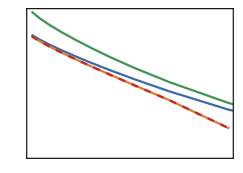

```mathematica
fig = ListLogPlot[
{
changelist@keyrate1listvarT,
changelist@keyrate2listvarT,
changelist@keyrate3listvarT,
changelist@keyrate4listvarT
}
,Joined->True, PlotStyle->{col1, col3, col2, {col4, Dashed}},
ImageSize->8.6cm,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\text{dB Loss}", ContentPadding->False, FontSize->fs1], MaTeX["\\kappa", ContentPadding->False, FontSize->fs1]},
PlotRange->{{0, 10}, All},
FrameTicks->{{
{{1.0, MaTeX["10^0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["5\\times 10^{-1}", ContentPadding->False, FontSize->fs2]},
{0.1, MaTeX["10^{-1}", ContentPadding->False, FontSize->fs2]},
{0.01, MaTeX["10^{-2}", ContentPadding->False, FontSize->fs2]},
{0.2, Null}, {0.3, Null}, {0.4, Null}, {0.6, Null},
{0.02, Null}, {0.03, Null}, {0.04, Null}, {0.05, MaTeX["5 \\times 10^{-2}", ContentPadding->False, FontSize->fs2]},{0.06, Null}, {0.07, Null}, {0.08, Null}, {0.09, Null},
{0.009, Null}, {0.008, Null}, {0.007, Null}, {0.006, Null}, {0.005, Null}
}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]},
{4.0, MaTeX["4.0", ContentPadding->False, FontSize->fs2]},
{6.0, MaTeX["6.0", ContentPadding->False, FontSize->fs2]},
{8.0, MaTeX["8.0", ContentPadding->False, FontSize->fs2]},
{10.0, MaTeX["10.0", ContentPadding->False, FontSize->fs2]}

},None}}
];
fig~Magnify~2
(*keyrate_honest_1.pdf*)
```

```mathematica
keyrate1listvarT2~Chop~(10^-8)
```

{{0.01,0.000920568},{0.1,0.0105236},{0.2,0.0219979},{0.3,0.0344926},{0.4,0.0479399},{0.5,0.062604},{0.6,0.0787131},{0.7,0.096542},{0.8,0.116573},{0.9,0.139711},{0.99,0.165844}}

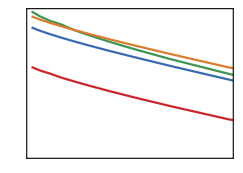

```mathematica
fig = ListLogPlot[
{
changelist@Chop[keyrate1listvarT2, 10^-8],
changelist@Chop[keyrate2listvarT2, 10^-8],
changelist@Chop[keyrate3listvarT2, 10^-8],
changelist@Chop[keyrate4listvarT2, 10^-8]
}
,Joined->True, PlotStyle->{col1, col3, col2, {col4}},
ImageSize->8.6cm,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\text{dB Loss}", ContentPadding->False, FontSize->fs1], MaTeX["\\kappa", ContentPadding->False, FontSize->fs1]},
PlotRange->{{0, 10}, All},
FrameTicks->{{
{{1.0, MaTeX["10^0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["5\\times 10^{-1}", ContentPadding->False, FontSize->fs2]},
{0.1, MaTeX["10^{-1}", ContentPadding->False, FontSize->fs2]},
{0.01, MaTeX["10^{-2}", ContentPadding->False, FontSize->fs2]},
{0.2, Null}, {0.3, Null}, {0.4, Null}, {0.6, Null},
{0.02, Null}, {0.03, Null}, {0.04, Null}, {0.05, MaTeX["5 \\times 10^{-2}", ContentPadding->False, FontSize->fs2]},{0.06, Null}, {0.07, Null}, {0.08, Null}, {0.09, Null},
{0.009, Null}, {0.008, Null}, {0.007, Null}, {0.006, Null}, {0.005, MaTeX["5\\times 10^{-3}", ContentPadding->False, FontSize->fs2]}, {0.004, Null}, {0.003, Null}, {0.002, Null}, {0.001, MaTeX["10^{-3}", ContentPadding->False, FontSize->fs2]},
{0.0009, Null}, {0.0008, Null}, {0.0007, Null}, {0.0006, Null}, {0.0005, MaTeX["5\\times 10^{-4}", ContentPadding->False, FontSize->fs2]}, {0.0004, Null}, {0.0003, Null}, {0.0002, Null}, {0.0001, MaTeX["10^{-4}", ContentPadding->False, FontSize->fs2]}
}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]},
{4.0, MaTeX["4.0", ContentPadding->False, FontSize->fs2]},
{6.0, MaTeX["6.0", ContentPadding->False, FontSize->fs2]},
{8.0, MaTeX["8.0", ContentPadding->False, FontSize->fs2]},
{10.0, MaTeX["10.0", ContentPadding->False, FontSize->fs2]}

},None}}
];
fig~Magnify~2
(*keyrate_dishonest_1.pdf*)
```

Making the graphs

## MutInf

### Exploring

```mathematica
(* 
graph1list; honest, symmetric g,h, scanning αb, αc;
graph1list2; honest, symmetric g,h, αb=αc, Tb=Tc, scanning α, T;
graph1list3; honest, asymmetric g,h, αb=αc, Tb=Tc, scanning α, T;

graph2list1; dishonest, symmetric g,h, scanning αb, αc;
graph2list2; dishonest, symmetric g,h, αb=αc, Tb=Tc, scanning α, T;
graph2list3; dishonest, asymmetric g,h, αb=αc, Tb=Tc, scanning α, T;
*)
ListPlot3D[
{
Flatten[graph1list,1],
Flatten[graph2list1,1]
}
]
```

-Graphics3D-

```mathematica
ListPlot3D[
{
Flatten[graph1list2,1]
}
]
```

-Graphics3D-

```mathematica
ListPlot3D[{Flatten[graph1list2,1][[;;,1]],Flatten[graph1list2,1][[;;,2]],Flatten[graph1list2,1][[;;,3]] - Flatten[graph1list3,1][[;;,3]]}//Transpose]
```

-Graphics3D-

```mathematica
ListPlot3D[
{
Flatten[graph1list2,1],
Flatten[graph2list2,1]
}
]
```

-Graphics3D-

### Making graphs for thesis

```mathematica
fs1=15;
fs2=10;
fig = ListPlot3D[
Flatten[graph1list2, 1],
Mesh->True,
AxesStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
AxesLabel->{
MaTeX["\\alpha", ContentPadding->False, FontSize->fs1],
MaTeX["T", ContentPadding->False, FontSize->fs1],
MaTeX["I", ContentPadding->False, FontSize->fs1]
},
Ticks->{
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]}
},
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["0.5", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
},
{
{0, MaTeX["0", ContentPadding->False, FontSize->fs2]},
{1, MaTeX["1", ContentPadding->False, FontSize->fs2]},
{2, MaTeX["2", ContentPadding->False, FontSize->fs2]}
}
},
PlotStyle->col1
];
fig~Magnify~2
(* mutinf_honest_symmetric_a_T.pdf *)
```

-Graphics3D-

```mathematica
fs1=15;
fs2=10;
fig1 = ListPlot3D[
{Flatten[graph1list2, 1](*,
Flatten[graph2list2, 1]*)},
Mesh->None,
AxesStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
AxesLabel->{
MaTeX["\\alpha", ContentPadding->False, FontSize->fs1],
MaTeX["T", ContentPadding->False, FontSize->fs1],
MaTeX["I", ContentPadding->False, FontSize->fs1]
},
Ticks->{
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]}
},
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["0.5", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
},
{
{0, MaTeX["0", ContentPadding->False, FontSize->fs2]},
{1, MaTeX["1", ContentPadding->False, FontSize->fs2]},
{2, MaTeX["2", ContentPadding->False, FontSize->fs2]}
}
},
PlotStyle->{{col1, Opacity[0.2]}, col2}
];
fig1~Magnify~2
```

-Graphics3D-

```mathematica
fs1=15;
fs2=10;
fig2= ListPlot3D[
{(*Flatten[graph1list2, 1],*)
Flatten[graph2list2, 1]},
Mesh->True,
AxesStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
AxesLabel->{
MaTeX["\\alpha", ContentPadding->False, FontSize->fs1],
MaTeX["T", ContentPadding->False, FontSize->fs1],
MaTeX["I", ContentPadding->False, FontSize->fs1]
},
Ticks->{
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]}
},
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["0.5", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
},
{
{0, MaTeX["0", ContentPadding->False, FontSize->fs2]},
{1, MaTeX["1", ContentPadding->False, FontSize->fs2]},
{2, MaTeX["2", ContentPadding->False, FontSize->fs2]}
}
},
PlotStyle->{ col2}
];
fig2~Magnify~2
```

-Graphics3D-

```mathematica
fig3=Show[fig1, fig2];
fig3~Magnify~2
(* mutinf_dishonest_symmetric_a_T_and_honest.pdf *)
```

-Graphics3D-

## Holevo

### Honest Bob/Charlie

```mathematica
gin = 0.5;
hin = 0.5;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
dimstest=8;
(*holevo1list2 = Monitor[Table[{α, T, honestHolevo[gin, hin, α, α, T, T, dimstest]},{α, αlist}, {T, Tlist}], "α = "<>ToString[α]<>", T = "<>ToString[T]]*)
```

```mathematica
holevo1list2={{{0.01,0.01,1.7739342131730187*^-7},{0.01,0.1,1.736583393951649*^-7},{0.01,0.2,1.6702636818511502*^-7},{0.01,0.30000000000000004,1.577057060558537*^-7},{0.01,0.4,1.4560046502167835*^-7},{0.01,0.5,1.3058939179349562*^-7},{0.01,0.6,1.1251177825738826*^-7},{0.01,0.7000000000000001,9.113947803591517*^-8},{0.01,0.8,6.611110119460542*^-8},{0.01,0.9,3.6721476395903604*^-8},{0.01,0.99,4.551201009757224*^-9}},{{0.1,0.01,0.000016309166724737256},{0.1,0.1,0.00007038039528786677},{0.1,0.2,0.00011989828933145485},{0.1,0.30000000000000004,0.00015781556625128756},{0.1,0.4,0.00018353234712893685},{0.1,0.5,0.00019630382859711637},{0.1,0.6,0.00019516431144468716},{0.1,0.7000000000000001,0.00017878202942738647},{0.1,0.8,0.00014512166832245793},{0.1,0.9,0.00009040452123904377},{0.1,0.99,0.000013068310523764882}},{{0.30000000000000004,0.01,0.00035131879667171795},{0.30000000000000004,0.1,0.0027877705008820808},{0.30000000000000004,0.2,0.005108464153580794},{0.30000000000000004,0.30000000000000004,0.006944704805211921},{0.30000000000000004,0.4,0.00826284861156601},{0.30000000000000004,0.5,0.009045718202652986},{0.30000000000000004,0.6,0.009177276133976286},{0.30000000000000004,0.7000000000000001,0.00860318271391386},{0.30000000000000004,0.8,0.007188674272010032},{0.30000000000000004,0.9,0.004673306275916583},{0.30000000000000004,0.99,0.0007538047259681574}},{{0.5,0.01,0.0016651173552382215},{0.5,0.1,0.014543035403989268},{0.5,0.2,0.026741329136420022},{0.5,0.30000000000000004,0.036355692492182845},{0.5,0.4,0.04332799429581846},{0.5,0.5,0.047455404277391366},{0.5,0.6,0.0484900576689955},{0.5,0.7000000000000001,0.04585742898926548},{0.5,0.8,0.038839696470642227},{0.5,0.9,0.025843272374397208},{0.5,0.99,0.004425265454354357}},{{0.7000000000000001,0.01,0.0045865209518498595},{0.7000000000000001,0.1,0.04120304115458051},{0.7000000000000001,0.2,0.07502995660295797},{0.7000000000000001,0.30000000000000004,0.10166440544884514},{0.7000000000000001,0.4,0.12065156514395525},{0.7000000000000001,0.5,0.13174907794124224},{0.7000000000000001,0.6,0.13430456336719532},{0.7000000000000001,0.7000000000000001,0.1271859212495754},{0.7000000000000001,0.8,0.10816728182748969},{0.7000000000000001,0.9,0.07294564125122621},{0.7000000000000001,0.99,0.013023570063598694}},{{0.9,0.01,0.009490609621400914},{0.9,0.1,0.08597704539506479},{0.9,0.2,0.15615577689747573},{0.9,0.30000000000000004,0.21039704410917848},{0.9,0.4,0.24862963417195827},{0.9,0.5,0.2700050729745449},{0.9,0.6,0.274189392816635},{0.9,0.7000000000000001,0.25901787963114864},{0.9,0.8,0.22040666570191103},{0.9,0.9,0.14941400297260143},{0.9,0.99,0.02745037966964667}},{{1.1,0.01,0.015931935389372764},{1.1,0.1,0.14682322329667263},{1.1,0.2,0.2669337151636557},{1.1,0.30000000000000004,0.35992613746180435},{1.1,0.4,0.42627860553996344},{1.1,0.5,0.4639331886398197},{1.1,0.6,0.4703794578272218},{1.1,0.7000000000000001,0.44286670398594796},{1.1,0.8,0.37574891917512176},{1.1,0.9,0.2545739205947084},{1.1,0.99,0.04764563184323853}},{{1.3000000000000003,0.01,0.023543105274121068},{1.3000000000000003,0.1,0.21648367380939204},{1.3000000000000003,0.2,0.39400127405985375},{1.3000000000000003,0.30000000000000004,0.5353849928944205},{1.3000000000000003,0.4,0.6392453725737894},{1.3000000000000003,0.5,0.7015107783589669},{1.3000000000000003,0.6,0.7163793890046195},{1.3000000000000003,0.7000000000000001,0.6766640674140203},{1.3000000000000003,0.8,0.5737688869678474},{1.3000000000000003,0.9,0.3885168809598867},{1.3000000000000003,0.99,0.073311968820436}},{{1.5,0.01,0.03183097156179571},{1.5,0.1,0.2886404368887314},{1.5,0.2,0.5228441846344842},{1.5,0.30000000000000004,0.7135712363582898},{1.5,0.4,0.8607256820197278},{1.5,0.5,0.9586426772847729},{1.5,0.6,0.9946270118987282},{1.5,0.7000000000000001,0.9524450348298741},{1.5,0.8,0.8132840846300522},{1.5,0.9,0.5502536788597305},{1.5,0.99,0.10465861715519131}}};
```

```mathematica
gin = 0.2;
hin = 0.8;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
dimstest=8;
(*holevo1list2 = Monitor[Table[{α, T, honestHolevo[gin, hin, α, α, T, T, dimstest]},{α, αlist}, {T, Tlist}], "α = "<>ToString[α]<>", T = "<>ToString[T]]*)
```

```mathematica
holevo1list2={{{0.01,0.01,-8.990668380962075*^-8},{0.01,0.1,-7.160092295671952*^-8},{0.01,0.2,-5.346413321566032*^-8},{0.01,0.30000000000000004,-3.768653323221391*^-8},{0.01,0.4,-2.4316453011959463*^-8},{0.01,0.5,-1.341151219269067*^-8},{0.01,0.6,-5.042904476816601*^-9},{0.01,0.7000000000000001,6.967173296623663*^-10},{0.01,0.8,3.6760144349074625*^-9},{0.01,0.9,3.6748664395259804*^-9},{0.01,0.99,6.384633501209836*^-10}},{{0.1,0.01,1.6191834633361157*^-6},{0.1,0.1,0.000056842158308562096},{0.1,0.2,0.00010766339281126358},{0.1,0.30000000000000004,0.00014691067754078746},{0.1,0.4,0.0001739869411192807},{0.1,0.5,0.00018815166798480387},{0.1,0.6,0.00018844581038418573},{0.1,0.7000000000000001,0.00017354862178190628},{0.1,0.8,0.00014144472588049212},{0.1,0.9,0.00008839965470132383},{0.1,0.99,0.000012956649415754844}},{{0.30000000000000004,0.01,0.00027042104173469195},{0.30000000000000004,0.1,0.002757077283860654},{0.30000000000000004,0.2,0.005086563879781125},{0.30000000000000004,0.30000000000000004,0.006932982315326797},{0.30000000000000004,0.4,0.008261751923581917},{0.30000000000000004,0.5,0.009028227700452529},{0.30000000000000004,0.6,0.009172333628089835},{0.30000000000000004,0.7000000000000001,0.008608062559295693},{0.30000000000000004,0.8,0.007199171444746522},{0.30000000000000004,0.9,0.004683304762181734},{0.30000000000000004,0.99,0.0007555100125576607}},{{0.5,0.01,0.0015050341174591697},{0.5,0.1,0.014513246655612155},{0.5,0.2,0.026722663218562204},{0.5,0.30000000000000004,0.03646088154526428},{0.5,0.4,0.0435713686275343},{0.5,0.5,0.047833612297856654},{0.5,0.6,0.048928711254875856},{0.5,0.7000000000000001,0.04637120996663091},{0.5,0.8,0.039349742832640144},{0.5,0.9,0.026224307885135634},{0.5,0.99,0.004492248649931495}},{{0.7000000000000001,0.01,0.004353929227715714},{0.7000000000000001,0.1,0.04114945683043114},{0.7000000000000001,0.2,0.07539968254328677},{0.7000000000000001,0.30000000000000004,0.10252546650995331},{0.7000000000000001,0.4,0.122244714809423},{0.7000000000000001,0.5,0.13408433645715578},{0.7000000000000001,0.6,0.1372764999257765},{0.7000000000000001,0.7000000000000001,0.1304510307648088},{0.7000000000000001,0.8,0.11151998223568482},{0.7000000000000001,0.9,0.07551611350648973},{0.7000000000000001,0.99,0.013496197795496517}},{{0.9,0.01,0.009203242693268443},{0.9,0.1,0.08607281699086489},{0.9,0.2,0.1570992463526495},{0.9,0.30000000000000004,0.21292924049854678},{0.9,0.4,0.2532928461090811},{0.9,0.5,0.27697628932395446},{0.9,0.6,0.283122527039936},{0.9,0.7000000000000001,0.26927222569828424},{0.9,0.8,0.23089921439646255},{0.9,0.9,0.15773732338687851},{0.9,0.99,0.02915450652495777}},{{1.1,0.01,0.015795265064117103},{1.1,0.1,0.14697011787490188},{1.1,0.2,0.2681918435760431},{1.1,0.30000000000000004,0.36378893544748525},{1.1,0.4,0.4330829434058945},{1.1,0.5,0.4746001933772712},{1.1,0.6,0.4857745155382487},{1.1,0.7000000000000001,0.46259081674483893},{1.1,0.8,0.3976544844589578},{1.1,0.9,0.2735633294808555},{1.1,0.99,0.051925640138073326}},{{1.3000000000000003,0.01,0.023403162284935775},{1.3000000000000003,0.1,0.21630904427503372},{1.3000000000000003,0.2,0.3946977241435561},{1.3000000000000003,0.30000000000000004,0.5369902916380052},{1.3000000000000003,0.4,0.643081003394621},{1.3000000000000003,0.5,0.7097220355778782},{1.3000000000000003,0.6,0.7315839832117255},{1.3000000000000003,0.7000000000000001,0.7010899525430987},{1.3000000000000003,0.8,0.6061438249359121},{1.3000000000000003,0.9,0.42027098164961807},{1.3000000000000003,0.99,0.08171508347875808}},{{1.5,0.01,0.03161161546497526},{1.5,0.1,0.28829846888210353},{1.5,0.2,0.5221625431997556},{1.5,0.30000000000000004,0.7105703925450371},{1.5,0.4,0.8556516396652158},{1.5,0.5,0.9537793603131952},{1.5,0.6,0.9955787490686285},{1.5,0.7000000000000001,0.9665725037523738},{1.5,0.8,0.8455969820498457},{1.5,0.9,0.5931387926609455},{1.5,0.99,0.11821988971951783}}};
```

### Dishonest Bob/Charlie

```mathematica
gin = 0.5;
hin = 0.5;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
(*Now
holevo2list2 = Monitor[Table[{α, T, dishonestHolevo[gin, hin, α, α, T, T, dimstest]},{α, αlist}, {T, Tlist}], "α = "<>ToString[α]<>", T = "<>ToString[T]]
Now*)
```

```mathematica
holevo2list2 = {{{0.01,0.01,1.6917552844871418*^-7},{0.01,0.1,1.6151141649556507*^-7},{0.01,0.2,1.5111056895556786*^-7},{0.01,0.30000000000000004,1.1209404872565033*^-7},{0.01,0.4,1.0188475477418239*^-7},{0.01,0.5,9.007562796906413*^-8},{0.01,0.6,7.65834957532378*^-8},{0.01,0.7000000000000001,6.127836004008076*^-8},{0.01,0.8,4.3944080049297674*^-8},{0.01,0.9,2.8582061006659446*^-8},{0.01,0.99,2.962942611405586*^-9}},{{0.1,0.01,0.000010736562650423553},{0.1,0.1,0.00003929433865301757},{0.1,0.2,0.00006369678527418099},{0.1,0.30000000000000004,0.00008230319760804683+8.981713321431704*^-10 ⅈ},{0.1,0.4,0.00009480251415314167+4.854764163235083*^-10 ⅈ},{0.1,0.5,0.00010082167850904156},{0.1,0.6,0.00009986433412018103},{0.1,0.7000000000000001,0.00009124035303867406},{0.1,0.8,0.00007392261568037184},{0.1,0.9,0.00004598566140103476},{0.1,0.99,6.714597368792565*^-6}},{{0.30000000000000004,0.01,0.00020014916612765+2.2181152281164707*^-9 ⅈ},{0.30000000000000004,0.1,0.0014412870557330426+2.6579630787341257*^-9 ⅈ},{0.30000000000000004,0.2,0.002610361135890804+1.0369318991145948*^-9 ⅈ},{0.30000000000000004,0.30000000000000004,0.003543274550423081+2.0643177923977985*^-9 ⅈ},{0.30000000000000004,0.4,0.004215543928405174+5.013216500792528*^-10 ⅈ},{0.30000000000000004,0.5,0.004610118281610731+2.270508492065403*^-9 ⅈ},{0.30000000000000004,0.6,0.004693606617187207+6.565308056792505*^-10 ⅈ},{0.30000000000000004,0.7000000000000001,0.004416165426358254+4.5958504443355676*^-10 ⅈ},{0.30000000000000004,0.8,0.0037042875801973907+4.6118754681751284*^-10 ⅈ},{0.30000000000000004,0.9,0.0024180449344855526},{0.30000000000000004,0.99,0.0003896657646377099}},{{0.5,0.01,0.000881689382375983+2.451118827344992*^-9 ⅈ},{0.5,0.1,0.007398310336175107+1.160439813801057*^-9 ⅈ},{0.5,0.2,0.013625883817342865+3.401479083480763*^-9 ⅈ},{0.5,0.30000000000000004,0.018618263229265186+1.7594345647830656*^-9 ⅈ},{0.5,0.4,0.02244812374762173+1.9168623792692932*^-9 ⅈ},{0.5,0.5,0.02485557003432548+3.486495081910602*^-9 ⅈ},{0.5,0.6,0.02561726827590799+1.9799441972395794*^-9 ⅈ},{0.5,0.7000000000000001,0.02446303929491689+1.1309064630271892*^-9 ⅈ},{0.5,0.8,0.020913242767022944+4.70972397982325*^-10 ⅈ},{0.5,0.9,0.014068736338592291+4.904132567828897*^-10 ⅈ},{0.5,0.99,0.0024399501361415214}},{{0.7000000000000001,0.01,0.002367079235832792+5.454037668749602*^-10 ⅈ},{0.7000000000000001,0.1,0.02094824606903334},{0.7000000000000001,0.2,0.03868639563140275+4.5414538479733676*^-10 ⅈ},{0.7000000000000001,0.30000000000000004,0.05330045984501042+1.1412908579545205*^-9 ⅈ},{0.7000000000000001,0.4,0.06422576097670629+3.115335026003417*^-9 ⅈ},{0.7000000000000001,0.5,0.07132190787298698+1.3505493259783436*^-9 ⅈ},{0.7000000000000001,0.6,0.07394199770243848+3.1462365016594316*^-9 ⅈ},{0.7000000000000001,0.7000000000000001,0.07122093270232599+2.2960132005367534*^-9 ⅈ},{0.7000000000000001,0.8,0.061726681439379205+2.9238338496270146*^-9 ⅈ},{0.7000000000000001,0.9,0.042426751127660756+1.0479536641682459*^-9 ⅈ},{0.7000000000000001,0.99,0.007747022060221792}},{{0.9,0.01,0.004842538948073738},{0.9,0.1,0.04396003381431246},{0.9,0.2,0.08171716012640773},{0.9,0.30000000000000004,0.11256060660271094},{0.9,0.4,0.13617410699641463+5.567940571642888*^-10 ⅈ},{0.9,0.5,0.151509459807734+5.569973092713014*^-10 ⅈ},{0.9,0.6,0.15750807547599832+1.0672940969338414*^-9 ⅈ},{0.9,0.7000000000000001,0.1511161111893431+2.4410795269363093*^-9 ⅈ},{0.9,0.8,0.13225833959504762+3.3974299258635632*^-9 ⅈ},{0.9,0.9,0.09243638524517+2.6579630930453722*^-9 ⅈ},{0.9,0.99,0.017611558450614594}},{{1.1,0.01,0.008177724255676644},{1.1,0.1,0.07562096851121103},{1.1,0.2,0.1415103751562723},{1.1,0.30000000000000004,0.19659892988333172},{1.1,0.4,0.23926714139749317},{1.1,0.5,0.2657242116137881},{1.1,0.6,0.2781962718260982+5.317683736005845*^-10 ⅈ},{1.1,0.7000000000000001,0.27083056166123554+5.243089990260702*^-10 ⅈ},{1.1,0.8,0.23819785788273418+2.936828012262795*^-9 ⅈ},{1.1,0.9,0.16819217239600376+1.6831058439851526*^-9 ⅈ},{1.1,0.99,0.033120495962862345+7.046333655115789*^-10 ⅈ}},{{1.3000000000000003,0.01,0.012014060758286371},{1.3000000000000003,0.1,0.11251953828390926},{1.3000000000000003,0.2,0.21197976275185448},{1.3000000000000003,0.30000000000000004,0.2972392631072134},{1.3000000000000003,0.4,0.3635770186440406},{1.3000000000000003,0.5,0.41228857077022485},{1.3000000000000003,0.6,0.435655735319449},{1.3000000000000003,0.7000000000000001,0.42999320202332925},{1.3000000000000003,0.8,0.37877646731374504+1.7315032819813468*^-9 ⅈ},{1.3000000000000003,0.9,0.26989235173619625+2.9942857096149583*^-9 ⅈ},{1.3000000000000003,0.99,0.05460838509591963+4.5439728415556435*^-10 ⅈ}},{{1.5,0.01,0.01615328332948307},{1.5,0.1,0.15147651991785382},{1.5,0.2,0.28620798305327266},{1.5,0.30000000000000004,0.4011557624378683},{1.5,0.4,0.5000331660270079},{1.5,0.5,0.5769053074886288},{1.5,0.6,0.6156770540945045},{1.5,0.7000000000000001,0.6128467356069597},{1.5,0.8,0.5491342882002057},{1.5,0.9,0.3958297730006227+1.160439813801057*^-9 ⅈ},{1.5,0.99,0.08212681734261915}}};
```

```mathematica
gin = 0.2;
hin = 0.8;
Tbin = 0.6;
Tcin = 0.6;
nbin = 0.0;
ncin=0.0;
(*Now
holevo2list3 = Monitor[Table[{α, T, dishonestHolevo[gin, hin, α, α, T, T, dimstest]},{α, αlist}, {T, Tlist}], "α = "<>ToString[α]<>", T = "<>ToString[T]]
Now*)
```

```mathematica
holevo2list3 = {{{0.01,0.01,-5.092565023973516*^-6},{0.01,0.1,-4.662495391163533*^-6},{0.01,0.2,-4.1814657737370906*^-6},{0.01,0.30000000000000004,-3.696459924103874*^-6},{0.01,0.4,-3.2066316719178527*^-6},{0.01,0.5,-2.7108427126423503*^-6},{0.01,0.6,-2.2074821437192103*^-6},{0.01,0.7000000000000001,-1.6940976577730369*^-6},{0.01,0.8,-1.1665013052355858*^-6},{0.01,0.9,-6.115726632653304*^-7},{0.01,0.99,-7.272176002455835*^-8}},{{0.1,0.01,-0.00027377390237807997},{0.1,0.1,-0.00020088037799860514},{0.1,0.2,-0.0001292995265275848},{0.1,0.30000000000000004,-0.00006801118118509447+8.981713321431704*^-10 ⅈ},{0.1,0.4,-0.000017495214379853463+4.854764163235083*^-10 ⅈ},{0.1,0.5,0.000021669286182045278},{0.1,0.6,0.00004873943461161656},{0.1,0.7000000000000001,0.00006271256363785463},{0.1,0.8,0.00006211998084725001},{0.1,0.9,0.000044334668088077955},{0.1,0.99,7.18478637555032*^-6}},{{0.30000000000000004,0.01,-0.0012656752344384903+2.2181152281164707*^-9 ⅈ},{0.30000000000000004,0.1,0.0011809583181680017+2.6579630787341257*^-9 ⅈ},{0.30000000000000004,0.2,0.004738563306101118+1.0369318991145948*^-9 ⅈ},{0.30000000000000004,0.30000000000000004,0.006485402803507456+2.0643177923977985*^-9 ⅈ},{0.30000000000000004,0.4,0.007746309016230246+5.013216500792528*^-10 ⅈ},{0.30000000000000004,0.5,0.008478467662482225+2.270508492065403*^-9 ⅈ},{0.30000000000000004,0.6,0.008624457701467442+6.565308056792505*^-10 ⅈ},{0.30000000000000004,0.7000000000000001,0.00810227916499906+4.5958504443355676*^-10 ⅈ},{0.30000000000000004,0.8,0.006782396287333806+4.6118754681751284*^-10 ⅈ},{0.30000000000000004,0.9,0.00441808169536774},{0.30000000000000004,0.99,0.0007132590092536074}},{{0.5,0.01,-0.0016126515799333996+2.451118827344992*^-9 ⅈ},{0.5,0.1,0.013557891214020068+1.160439813801057*^-9 ⅈ},{0.5,0.2,0.025099926029998887+3.401479083480763*^-9 ⅈ},{0.5,0.30000000000000004,0.034339078549700086+1.7594345647830656*^-9 ⅈ},{0.5,0.4,0.04113522380700019+1.9168623792692932*^-9 ⅈ},{0.5,0.5,0.04523269344113845+3.486495081910602*^-9 ⅈ},{0.5,0.6,0.04635020073936136+1.9799441972395794*^-9 ⅈ},{0.5,0.7000000000000001,0.04398991359768423+1.1309064630271892*^-9 ⅈ},{0.5,0.8,0.03738138849439043+4.70972397982325*^-10 ⅈ},{0.5,0.9,0.024947588550552235+4.904132567828897*^-10 ⅈ},{0.5,0.99,0.0042794663469097015}},{{0.7000000000000001,0.01,-0.0003573410004360511+5.454037668749602*^-10 ⅈ},{0.7000000000000001,0.1,0.03863148639431313},{0.7000000000000001,0.2,0.07113407251923332+4.5414538479733676*^-10 ⅈ},{0.7000000000000001,0.30000000000000004,0.09700480084307594+1.1412908579545205*^-9 ⅈ},{0.7000000000000001,0.4,0.11598622068631437+3.115335026003417*^-9 ⅈ},{0.7000000000000001,0.5,0.12753205999333517+1.3505493259783436*^-9 ⅈ},{0.7000000000000001,0.6,0.1308820296353923+3.1462365016594316*^-9 ⅈ},{0.7000000000000001,0.7000000000000001,0.12476007976291048+2.2960132005367534*^-9 ⅈ},{0.7000000000000001,0.8,0.10692075085540165+2.9238338496270146*^-9 ⅈ},{0.7000000000000001,0.9,0.07252134785999967+1.0479536641682459*^-9 ⅈ},{0.7000000000000001,0.99,0.012943036858716776}},{{0.9,0.01,0.0030773229830207693},{0.9,0.1,0.08106197149174377},{0.9,0.2,0.14861387883127808},{0.9,0.30000000000000004,0.20213033859224638},{0.9,0.4,0.24115495287875421+5.567940571642888*^-10 ⅈ},{0.9,0.5,0.26481000095907725+5.569973092713014*^-10 ⅈ},{0.9,0.6,0.2716686273184734+1.0672940969338414*^-9 ⅈ},{0.9,0.7000000000000001,0.25809254340129406+2.4410795269363093*^-9 ⅈ},{0.9,0.8,0.22238528595418172+3.3974299258635632*^-9 ⅈ},{0.9,0.9,0.1526208581652329+2.6579630930453722*^-9 ⅈ},{0.9,0.99,0.028350201643976773}},{{1.1,0.01,0.014615330704633056},{1.1,0.1,0.13861018467979047},{1.1,0.2,0.25409248884376634},{1.1,0.30000000000000004,0.3460596518853505},{1.1,0.4,0.4136155488474065},{1.1,0.5,0.45309732858338825},{1.1,0.6,0.4663847089570121+5.317683736005845*^-10 ⅈ},{1.1,0.7000000000000001,0.4472178041750762+5.243089990260702*^-10 ⅈ},{1.1,0.8,0.3861169236806771+2.936828012262795*^-9 ⅈ},{1.1,0.9,0.2668021432943766+1.6831058439851526*^-9 ⅈ},{1.1,0.99,0.05082427120706227+7.046333655115789*^-10 ⅈ}},{{1.3000000000000003,0.01,0.021763609082815938},{1.3000000000000003,0.1,0.20429351727088974},{1.3000000000000003,0.2,0.3742457760384801},{1.3000000000000003,0.30000000000000004,0.5113109880515132},{1.3000000000000003,0.4,0.6123552675429902},{1.3000000000000003,0.5,0.679333393541639},{1.3000000000000003,0.6,0.703942303845312},{1.3000000000000003,0.7000000000000001,0.6774679512608397},{1.3000000000000003,0.8,0.5885680686871977+1.7315032819813468*^-9 ⅈ},{1.3000000000000003,0.9,0.41019451650096433+2.9942857096149583*^-9 ⅈ},{1.3000000000000003,0.99,0.08005724592237967+4.5439728415556435*^-10 ⅈ}},{{1.5,0.01,0.029488612543424386},{1.5,0.1,0.2726134218882741},{1.5,0.2,0.49605429521339217},{1.5,0.30000000000000004,0.6747266725417687},{1.5,0.4,0.8169246014339797},{1.5,0.5,0.9120430395363268},{1.5,0.6,0.953745877213103},{1.5,0.7000000000000001,0.9287621258521657},{1.5,0.8,0.8159767566448741},{1.5,0.9,0.575400098137949+1.160439813801057*^-9 ⅈ},{1.5,0.99,0.11502975158682568}}};
```

### Making the graphs

```mathematica
fs1=15;
fs2=10;
fig = ListPlot3D[
Flatten[holevo1list2, 1],
Mesh->True,
AxesStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
AxesLabel->{
MaTeX["\\alpha", ContentPadding->False, FontSize->fs1],
MaTeX["T", ContentPadding->False, FontSize->fs1],
MaTeX["I", ContentPadding->False, FontSize->fs1]
},
Ticks->{
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]}
},
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["0.5", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
},
{
{0, MaTeX["0", ContentPadding->False, FontSize->fs2]},
{1, MaTeX["1", ContentPadding->False, FontSize->fs2]},
{2, MaTeX["2", ContentPadding->False, FontSize->fs2]}
}
},
PlotStyle->col1
];
fig~Magnify~2
(* holevo_honest_symmetric_a_T.pdf *)
```

-Graphics3D-

```mathematica
fs1=15;
fs2=10;
fig1 = ListPlot3D[
{Flatten[holevo1list2, 1](*,
Flatten[graph2list2, 1]*)},
Mesh->None,
AxesStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
AxesLabel->{
MaTeX["\\alpha", ContentPadding->False, FontSize->fs1],
MaTeX["T", ContentPadding->False, FontSize->fs1],
MaTeX["I", ContentPadding->False, FontSize->fs1]
},
Ticks->{
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]}
},
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["0.5", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
},
{
{0, MaTeX["0", ContentPadding->False, FontSize->fs2]},
{1, MaTeX["1", ContentPadding->False, FontSize->fs2]},
{2, MaTeX["2", ContentPadding->False, FontSize->fs2]}
}
},
PlotStyle->{{col1, Opacity[0.2]}, col2}
];
fig1~Magnify~2
```

-Graphics3D-

```mathematica
fs1=15;
fs2=10;
fig2= ListPlot3D[
{(*Flatten[holevo1list2, 1],*)
Flatten[holevo2list2, 1]},
Mesh->True,
AxesStyle->BlackFrame,
BaseStyle->style,
ImageSize->8.6cm,
AspectRatio->1/1.4,
AxesLabel->{
MaTeX["\\alpha", ContentPadding->False, FontSize->fs1],
MaTeX["T", ContentPadding->False, FontSize->fs1],
MaTeX["I", ContentPadding->False, FontSize->fs1]
},
Ticks->{
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]}
},
{
{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{0.5, MaTeX["0.5", ContentPadding->False, FontSize->fs2]},
{1.0, MaTeX["1.0", ContentPadding->False, FontSize->fs2]}
},
{
{0, MaTeX["0", ContentPadding->False, FontSize->fs2]},
{1, MaTeX["1", ContentPadding->False, FontSize->fs2]},
{2, MaTeX["2", ContentPadding->False, FontSize->fs2]}
}
},
PlotStyle->{ col2}
];
fig2~Magnify~2
```

-Graphics3D-

```mathematica
fig3=Show[fig1, fig2];
fig3~Magnify~2
(* holevo_dishonest_symmetric_a_T_and_honest.pdf *)
```

-Graphics3D-

2020-03-05

## New “highly asymmetric” key rate graphs

```mathematica
(*honestKeyRate[gglob_, hglob_, βk_, cohampc_, Tb_, Tc_, dims_]
dishonestKeyRate[gglob_, hglob_, βk_, cohampc_, Tb_, Tc_, nb_, nc_, dims_]*)
```

```mathematica
dblist = Join[{0.01},Range[1, 20, 1.0]]
dimstest=8;
```

{0.01,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.}

```mathematica
(*list1 = Monitor[Table[
{db, honestKeyRate[0.2, 0.8, 0.3, 0.6,db2T[db], 0.7, dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
list1 = {{0.01,0.22215180063290507},{1.,0.22044636003813323},{2.,0.21930353949151704},{3.,0.21847458217263488},{4.,0.21785565395447892},{5.,0.21738576359054057},{6.,0.21702502579565203},{7.,0.2167458745070756},{8.,0.21652858287544624},{9.,0.21635868829951244},{10.,0.21622539780012112},{11.,0.21612054800352581},{12.,0.21603790016404484},{13.,0.21597264771794356},{14.,0.21592106392472749},{15.,0.21588024477146533},{16.,0.21584791836326855},{17.,0.2158223017433354},{18.,0.21580199218111112},{19.,0.21578588390507736},{20.,0.21577310386861975}};
```

```mathematica
(*list2 = Monitor[Table[
{db, honestKeyRate[0.3, 0.7, 0.3, 0.6,db2T[db], 0.7, dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
list2 = {{0.01,0.21949028557890432},{1.,0.21498014505615265},{2.,0.21195380152176135},{3.,0.20975693808126494},{4.,0.20811577508558937},{5.,0.20698777653894018},{6.,0.20603277516930918},{7.,0.20529358028334793},{8.,0.2047180791330131},{9.,0.2042680415568316},{10.,0.2039149229171115},{11.,0.20363712413875118},{12.,0.2034181327918636},{13.,0.2032452235610162},{14.,0.2031085277432625},{15.,0.2030003538982138},{16.,0.2029146839146197},{17.,0.20284679430036068},{18.,0.20279296853117046},{19.,0.2027502766560726},{20.,0.20271640523566536}};
```

```mathematica
(*list31 = Monitor[Table[
{db, dishonestKeyRate[0.2, 0.8, 0.3, 0.6,db2T[db], 0.7,0.0, 0.0, dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
list31 = {{0.01,0.22868860756783116},{1.,0.22867787033298353-4.999702262808321*^-10 ⅈ},{2.,0.22867649439573762-1.1259420900014033*^-9 ⅈ},{3.,0.22867781369359752-2.003787374874045*^-9 ⅈ},{4.,0.22867807171344773-2.042585047017808*^-9 ⅈ},{5.,0.22867829618958868-2.0417124607870505*^-9 ⅈ},{6.,0.22867845088450284-1.7408394904124988*^-9 ⅈ},{7.,0.22867854892385292-1.1061410314703922*^-9 ⅈ},{8.,0.2286786752510509-1.6188898635797111*^-9 ⅈ},{9.,0.228689829909556-1.5827710473521628*^-9 ⅈ},{10.,0.22868988996329442-2.01283132781731*^-9 ⅈ},{11.,0.22868993857831993-1.6521827060656317*^-9 ⅈ},{12.,0.2286899758764474-5.587677040008045*^-10 ⅈ},{13.,0.2286900104990664-1.0675990884377832*^-9 ⅈ},{14.,0.2286900388181458-1.119365939114812*^-9 ⅈ},{15.,0.22869006129129443-1.6240178094020513*^-9 ⅈ},{16.,0.2286900800691905-1.6729789590995602*^-9 ⅈ},{17.,0.22869009488061026-1.712792565140409*^-9 ⅈ},{18.,0.22869010673593493-1.7450107980022953*^-9 ⅈ},{19.,0.2286901167716714-1.770982114595227*^-9 ⅈ},{20.,0.2286901236925037-1.791854147724335*^-9 ⅈ}};
```

```mathematica
(*list32 = Monitor[Table[
{db, dishonestKeyRate[0.8, 0.2, 0.3, 0.6, db2T[db], 0.7,0.0, 0.0,  dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)

list32 = {{0.01,0.015712439468100747},{1.,0.015718762425380617-4.999702262808321*^-10 ⅈ},{2.,0.015724397554698233-1.1259420900014033*^-9 ⅈ},{3.,0.01572920283602075-2.003787374874045*^-9 ⅈ},{4.,0.015741983564187434-2.042585047017808*^-9 ⅈ},{5.,0.015736017720017648-2.0417124607870505*^-9 ⅈ},{6.,0.01573856446338817-1.7408394904124988*^-9 ⅈ},{7.,0.015740100246890876-1.1061410314703922*^-9 ⅈ},{8.,0.015741715579468907-1.6188898635797111*^-9 ⅈ},{9.,0.015773799727243132-1.5827710473521628*^-9 ⅈ},{10.,0.01577495097184156-2.01283132781731*^-9 ⅈ},{11.,0.01577588512029704-1.6521827060656317*^-9 ⅈ},{12.,0.01579234291917242-5.587677040008045*^-10 ⅈ},{13.,0.01579300344588519-1.0675990884377832*^-9 ⅈ},{14.,0.015809366710032524-1.119365939114812*^-9 ⅈ},{15.,0.015809853360373882-1.6240178094020513*^-9 ⅈ},{16.,0.01581052738054811-1.6729789590995602*^-9 ⅈ},{17.,0.01581049743996421-1.712792565140409*^-9 ⅈ},{18.,0.01581072380071591-1.7450107980022953*^-9 ⅈ},{19.,0.01581092153383956-1.770982114595227*^-9 ⅈ},{20.,0.01581105969240615-1.791854147724335*^-9 ⅈ}};
```

```mathematica
(*symmlist1 =  Monitor[Table[
{db, dishonestKeyRate[0.5, 0.5, 0.3, 0.6, 0.7, db2T[db], 0.0, 0.0, dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
symmlist1 = {{0.01,0.23680780133538826},{1.,0.15434838914550653-1.5330250421298659*^-9 ⅈ},{2.,0.10953891140183969-2.5531120751762336*^-9 ⅈ},{3.,0.08026404112381158-2.0025709486397713*^-9 ⅈ},{4.,0.059977993423305564-1.5935797885817125*^-9 ⅈ},{5.,0.04547297347872448-1.0309612089422868*^-9 ⅈ},{6.,0.0348179405444895-1.5157785997055939*^-9 ⅈ},{7.,0.02685266488796334-1.7290986641778363*^-9 ⅈ},{8.,0.020856969507325518-4.598805068342339*^-10 ⅈ},{9.,0.016222746691534784-9.613457120963713*^-10 ⅈ},{10.,0.01268742533594347-2.489237991321647*^-9 ⅈ},{11.,0.009948733371580643-2.5318677075234665*^-9 ⅈ},{12.,0.00781633850482999-2.1295036227903074*^-9 ⅈ},{13.,0.006125211208901193-2.1158814117178686*^-9 ⅈ},{14.,0.0048175084166790505-3.1199174500175103*^-9 ⅈ},{15.,0.0037891825077664976-3.209714776317487*^-9 ⅈ},{16.,0.002978886029757044-3.2833495643363462*^-9 ⅈ},{17.,0.002339341019255814-2.752639264398618*^-9 ⅈ},{18.,0.0018339059583216688-2.1802837980706192*^-9 ⅈ},{19.,0.0014340429149544143-2.204442037995011*^-9 ⅈ},{20.,0.0011174364693460337-2.6808779300399764*^-9 ⅈ}};
```

```mathematica
(*symmlist2=  Monitor[Table[
{db, dishonestKeyRate[0.5, 0.5, 0.3, 0.6, db2T[db], db2T[db], 0.0, 0.0, dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
symmlist2 = {{0.01,0.23680721358266144},{1.,0.1543511475343201-5.027016227735268*^-10 ⅈ},{2.,0.10953721031518493-2.0141783015478436*^-9 ⅈ},{3.,0.0802580049810181-1.6228384470655295*^-9 ⅈ},{4.,0.05995831465917789-9.868442925521208*^-10 ⅈ},{5.,0.045461164181406444-2.66212300647153*^-9 ⅈ},{6.,0.03479424480085114-1.6489832541046032*^-9 ⅈ},{7.,0.02683545931174247-1.5360391958450182*^-9 ⅈ},{8.,0.02081965434043742-1.2121949905029008*^-9 ⅈ},{9.,0.0162260676427457-2.1514520460347194*^-9 ⅈ},{10.,0.012662349079415991-2.596006072461666*^-9 ⅈ},{11.,0.009922878415526526-2.9120715651477503*^-9 ⅈ},{12.,0.007763687826607413-2.1456219466696196*^-9 ⅈ},{13.,0.006095864706449516-2.0834155830029985*^-9 ⅈ},{14.,0.004787756090129935-3.203973837887591*^-9 ⅈ},{15.,0.003759244756154745-3.1774081731292483*^-9 ⅈ},{16.,0.0029486244486405244-2.505606688146892*^-9 ⅈ},{17.,0.0023089169927184017-2.609899140726013*^-9 ⅈ},{18.,0.0018033713870457824-2.6954247787066824*^-9 ⅈ},{19.,0.0014034374714313458-3.2216732597469056*^-9 ⅈ},{20.,0.0010867888601822084-3.749081347045873*^-9 ⅈ}};
```

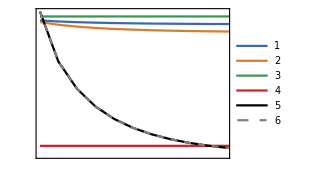

```mathematica
fs1=15;
fs2=10;
fig = ListPlot[
{
list1, 
list2,
Chop[list31,10^-8],
Chop[list32,10^-8],
Chop[symmlist1, 10^-8],
Chop[symmlist2, 10^-8]
},
Joined->True,
PlotStyle->{col1, col2, col3, col4, Black, {Gray, Dashed}},
PlotLegends->Automatic,
ImageSize->8.6cm,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\text{dB Loss}", ContentPadding->False, FontSize->fs1], MaTeX["\\kappa", ContentPadding->False, FontSize->fs1]},
PlotRange->{{0, 10}, All},
FrameTicks->{{
{
{0.0, MaTeX[ "0.0", ContentPadding->False, FontSize->fs2]},{0.1,MaTeX[ "0.1", ContentPadding->False, FontSize->fs2]},
{0.2,MaTeX[ "0.2", ContentPadding->False, FontSize->fs2]},
{0.3,MaTeX[ "0.3", ContentPadding->False, FontSize->fs2]},
{0.4,MaTeX[ "0.4", ContentPadding->False, FontSize->fs2]}
}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]},
{4.0, MaTeX["4.0", ContentPadding->False, FontSize->fs2]},
{6.0, MaTeX["6.0", ContentPadding->False, FontSize->fs2]},
{8.0, MaTeX["8.0", ContentPadding->False, FontSize->fs2]},
{10.0, MaTeX["10.0", ContentPadding->False, FontSize->fs2]}

},None}}
];
fig~Magnify~1
(* asymmetric_keyrates_1.pdf *)

(* Ah, this graph is nice because it shows little variation with loss, since the loss variation is on the party who has smallest share of final key. Let's make another one varying loss on the party who has the largest share *)
```

```mathematica
(*againlist1 = Monitor[Table[
{db, honestKeyRate[0.2, 0.8, 0.3, 0.6,0.7, db2T[db], dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
againlist1 = {{0.01,0.4054652776873393},{1.,0.2660563565084498},{2.,0.189535652419632},{3.,0.13912824975011395},{4.,0.10395424939351297},{5.,0.07859154757589573},{6.,0.05989387427938604},{7.,0.04588488463840035},{8.,0.03525881906498475},{9.,0.027583107761278},{10.,0.02131198809793467},{11.,0.0164445578371439},{12.,0.012648695638540444},{13.,0.009677331841522249},{14.,0.007344401543676368},{15.,0.0055083595786417396},{16.,0.004060631740799611},{17.,0.0029173680931125663},{18.,0.0020134543671452843},{19.,0.0012980987522605864},{20.,0.000731537971262187}};
```

```mathematica
(*againlist2 = Monitor[Table[
{db, honestKeyRate[0.3, 0.7, 0.3, 0.6,0.7, db2T[db], dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
againlist2 = {{0.01,0.3888319982534032},{1.,0.26065966863116813},{2.,0.1900493987547509},{3.,0.14346509854748277},{4.,0.11091783608265612},{5.,0.08741295680396},{6.,0.07007563329255898},{7.,0.05707086675717975},{8.,0.04719944503826046},{9.,0.03963534720461129},{10.,0.03379611637455472},{11.,0.029261916424792783},{12.,0.025724667182066716},{13.,0.02295494851785755},{14.,0.020779835026469448},{15.,0.019067678984030906},{16.,0.017717435001005227},{17.,0.01665102699494945},{18.,0.015807798499951717},{19.,0.016211699939076164},{20.,0.01570424863993922}};
```

```mathematica
(*againlist31 = Monitor[Table[
{db, dishonestKeyRate[0.2, 0.8, 0.3, 0.6,0.7, db2T[db],0.0, 0.0, dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
againlist31 = {{0.01,0.41667123005264545},{1.,0.27579272016072615-1.5330250421298659*^-9 ⅈ},{2.,0.19784669782824915-2.5531120751762336*^-9 ⅈ},{3.,0.1462439271427276-2.0025709486397713*^-9 ⅈ},{4.,0.11009032943726504-1.5935797885817125*^-9 ⅈ},{5.,0.08393269107844714-1.0309612089422868*^-9 ⅈ},{6.,0.0645932020904767-1.5157785997055939*^-9 ⅈ},{7.,0.050068801827974574-1.7290986641778363*^-9 ⅈ},{8.,0.0390299795426472-4.598805068342339*^-10 ⅈ},{9.,0.030562552725498016-9.613457120963713*^-10 ⅈ},{10.,0.024020462694256617-2.489237991321647*^-9 ⅈ},{11.,0.018936970795833785-2.5318677075234665*^-9 ⅈ},{12.,0.014968959947685212-2.1295036227903074*^-9 ⅈ},{13.,0.011860574716178851-2.1158814117178686*^-9 ⅈ},{14.,0.009418652648874648-3.1199174500175103*^-9 ⅈ},{15.,0.007495891264963861-3.209714776317487*^-9 ⅈ},{16.,0.0059792117411001655-3.2833495643363462*^-9 ⅈ},{17.,0.0047811210197514775-2.752639264398618*^-9 ⅈ},{18.,0.003833637365629361-2.1802837980706192*^-9 ⅈ},{19.,0.0030836542333823047-2.204442037995011*^-9 ⅈ},{20.,0.002489576115648262-2.6808779300399764*^-9 ⅈ}};
```

```mathematica
(*againlist32 = Monitor[Table[
{db, dishonestKeyRate[0.8, 0.2, 0.3, 0.6, 0.7, db2T[db],0.0, 0.0,  dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
againlist32 = {{0.01,0.029987381074619172},{1.,0.019203481764364427-1.5330250421298659*^-9 ⅈ},{2.,0.013478610575766825-2.5531120751762336*^-9 ⅈ},{3.,0.009797410361426784-2.0025709486397713*^-9 ⅈ},{4.,0.0072773232528428045-1.5935797885817125*^-9 ⅈ},{5.,0.005488703863896993-1.0309612089422868*^-9 ⅈ},{6.,0.00418747934420638-1.5157785997055939*^-9 ⅈ},{7.,0.0032233258527829545-1.7290986641778363*^-9 ⅈ},{8.,0.0024987371371939515-4.598805068342339*^-10 ⅈ},{9.,0.0019480691651281301-9.613457120963713*^-10 ⅈ},{10.,0.00152584564567948-2.489237991321647*^-9 ⅈ},{11.,0.0011997871097177981-2.5318677075234665*^-9 ⅈ},{12.,0.0009465624197004807-2.1295036227903074*^-9 ⅈ},{13.,0.0007490028783954106-2.1158814117178686*^-9 ⅈ},{14.,0.0005943119946298925-3.1199174500175103*^-9 ⅈ},{15.,0.00047282695094730265-3.209714776317487*^-9 ⅈ},{16.,0.00037720409203267913-3.2833495643363462*^-9 ⅈ},{17.,0.0003017948835624118-2.752639264398618*^-9 ⅈ},{18.,0.00024224080637336165-2.1802837980706192*^-9 ⅈ},{19.,0.00019515098847655565-2.204442037995011*^-9 ⅈ},{20.,0.00015788281035722385-2.6808779300399764*^-9 ⅈ}};
```

```mathematica
(*symmetriclist1 = Monitor[Table[
{db, dishonestKeyRate[0.5, 0.5, 0.3, 0.6, 0.7, db2T[db],0.0, 0.0,  dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
symmetriclist1 = {{0.01,0.23680780133538826},{1.,0.15434838914550653-1.5330250421298659*^-9 ⅈ},{2.,0.10953891140183969-2.5531120751762336*^-9 ⅈ},{3.,0.08026404112381158-2.0025709486397713*^-9 ⅈ},{4.,0.059977993423305564-1.5935797885817125*^-9 ⅈ},{5.,0.04547297347872448-1.0309612089422868*^-9 ⅈ},{6.,0.0348179405444895-1.5157785997055939*^-9 ⅈ},{7.,0.02685266488796334-1.7290986641778363*^-9 ⅈ},{8.,0.020856969507325518-4.598805068342339*^-10 ⅈ},{9.,0.016222746691534784-9.613457120963713*^-10 ⅈ},{10.,0.01268742533594347-2.489237991321647*^-9 ⅈ},{11.,0.009948733371580643-2.5318677075234665*^-9 ⅈ},{12.,0.00781633850482999-2.1295036227903074*^-9 ⅈ},{13.,0.006125211208901193-2.1158814117178686*^-9 ⅈ},{14.,0.0048175084166790505-3.1199174500175103*^-9 ⅈ},{15.,0.0037891825077664976-3.209714776317487*^-9 ⅈ},{16.,0.002978886029757044-3.2833495643363462*^-9 ⅈ},{17.,0.002339341019255814-2.752639264398618*^-9 ⅈ},{18.,0.0018339059583216688-2.1802837980706192*^-9 ⅈ},{19.,0.0014340429149544143-2.204442037995011*^-9 ⅈ},{20.,0.0011174364693460337-2.6808779300399764*^-9 ⅈ}};
```

```mathematica
(*symmetriclist2 = Monitor[Table[
{db, dishonestKeyRate[0.5, 0.5, 0.3, 0.6, db2T[db], db2T[db],0.0, 0.0,  dimstest]},
{db, dblist}
],
Row[{ProgressIndicator[Position[dblist, db][[1,1]], {1, Length[dblist]}], db}]
]*)
symmetriclist2 = {{0.01,0.23680721358266144},{1.,0.1543511475343201-5.027016227735268*^-10 ⅈ},{2.,0.10953721031518493-2.0141783015478436*^-9 ⅈ},{3.,0.0802580049810181-1.6228384470655295*^-9 ⅈ},{4.,0.05995831465917789-9.868442925521208*^-10 ⅈ},{5.,0.045461164181406444-2.66212300647153*^-9 ⅈ},{6.,0.03479424480085114-1.6489832541046032*^-9 ⅈ},{7.,0.02683545931174247-1.5360391958450182*^-9 ⅈ},{8.,0.02081965434043742-1.2121949905029008*^-9 ⅈ},{9.,0.0162260676427457-2.1514520460347194*^-9 ⅈ},{10.,0.012662349079415991-2.596006072461666*^-9 ⅈ},{11.,0.009922878415526526-2.9120715651477503*^-9 ⅈ},{12.,0.007763687826607413-2.1456219466696196*^-9 ⅈ},{13.,0.006095864706449516-2.0834155830029985*^-9 ⅈ},{14.,0.004787756090129935-3.203973837887591*^-9 ⅈ},{15.,0.003759244756154745-3.1774081731292483*^-9 ⅈ},{16.,0.0029486244486405244-2.505606688146892*^-9 ⅈ},{17.,0.0023089169927184017-2.609899140726013*^-9 ⅈ},{18.,0.0018033713870457824-2.6954247787066824*^-9 ⅈ},{19.,0.0014034374714313458-3.2216732597469056*^-9 ⅈ},{20.,0.0010867888601822084-3.749081347045873*^-9 ⅈ}};
```

#### Let us make some graphs

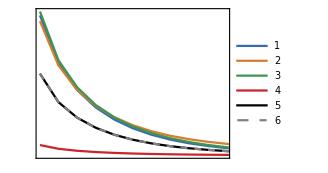

```mathematica
fs1=15;
fs2=10;
fig = ListPlot[
{
againlist1, 
againlist2,
Chop[againlist31,10^-8],
Chop[againlist32,10^-8],
Chop[symmetriclist1, 10^-8],
Chop[symmetriclist2, 10^-8]
},
Joined->True,
PlotStyle->{col1, col2, col3, col4, Black, {Gray, Dashed}},
PlotLegends->Automatic,
ImageSize->8.6cm,
Frame->True,
FrameStyle->BlackFrame,
BaseStyle->style,
AspectRatio->1/1.4,
FrameLabel->{MaTeX["\\text{dB Loss}", ContentPadding->False, FontSize->fs1], MaTeX["\\kappa", ContentPadding->False, FontSize->fs1]},
PlotRange->{{0, 10}, All},
FrameTicks->{{
{
{0.0, MaTeX[ "0.0", ContentPadding->False, FontSize->fs2]},{0.1,MaTeX[ "0.1", ContentPadding->False, FontSize->fs2]},
{0.2,MaTeX[ "0.2", ContentPadding->False, FontSize->fs2]},
{0.3,MaTeX[ "0.3", ContentPadding->False, FontSize->fs2]},
{0.4,MaTeX[ "0.4", ContentPadding->False, FontSize->fs2]}
}, None},
{{{0.0, MaTeX["0.0", ContentPadding->False, FontSize->fs2]},
{2.0, MaTeX["2.0", ContentPadding->False, FontSize->fs2]},
{4.0, MaTeX["4.0", ContentPadding->False, FontSize->fs2]},
{6.0, MaTeX["6.0", ContentPadding->False, FontSize->fs2]},
{8.0, MaTeX["8.0", ContentPadding->False, FontSize->fs2]},
{10.0, MaTeX["10.0", ContentPadding->False, FontSize->fs2]}

},None}}
];
(* asymmetric_keyrates_2.pdf *)
fig~Magnify~1
```